```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
SetOptions[{DensityPlot,ListLogPlot,ListLogLogPlot,Plot,LogPlot,LogLogPlot,ContourPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica",FontSize->16},Frame->True,AspectRatio->.8,FrameStyle->Directive[Black],ImagePadding->{{90,20},{60,50}},ImageSize->500];
<<MaTeX`;
SetOptions[MaTeX,Magnification->1.5];
```

## Constants

```mathematica
Element[Fv|A1|A2|A3|FT1|FT2|FT3,Complexes];
Element[s|t|mp|mV|mτ|GF|Vckm|SEW|ϵR|ϵT,Reals];
```

```mathematica
GeV=1.0;
MeV=10.^-3;
```

```mathematica
seg=10.^25/(6.58*GeV);
```

```mathematica
ττ=290.3*10^-15 seg;
```

```mathematica
NVALUESωπ={GF->1.1663788*10.^-5 GeV,Vckm->0.97373,SEW->1.0201,mτ->1.77686 GeV,mp->.13957039GeV,mV->.78266 GeV};
NVALUESωK={GF->1.1663788*10.^-5 GeV,Vckm->0.22534,SEW->1.0201,mτ->1.77686 GeV,mp->.4937GeV,mV->.78266 GeV};
NVALUESρK={GF->1.1663788*10.^-5 GeV,Vckm->0.22534,SEW->1.0201,mτ->1.77686 GeV,mp->.4937GeV,mV->.77526 GeV};
NVALUESKsπ={GF->1.1663788*10.^-5 GeV,Vckm->0.22534,SEW->1.0201,mτ->1.77686 GeV,mp->.13957039GeV,mV->.89166 GeV};
NVALUESKsK={GF->1.1663788*10.^-5 GeV,Vckm->0.97373,SEW->1.0201,mτ->1.77686 GeV,mp->.4937GeV,mV->.89166 GeV};
```

## Kinematics

Here we define the dot products of the external 4-momentums in terms of the correspoding independent variables in the phase space of 2,3 and 4 bodys.

```mathematica
λp[a_,b_,c_]:=a^2+b^2+c^2-2(a b + a c + b c);(*This definition will be usefull in the following*)
```

```mathematica
smin[x_,y_]:=(x+y)^2;
smax[x_,y_]:=(x-y)^2;
```

### 3-body phase space

Let use the convention α(p0)→β(p1)+γ(p2)+δ(p3) where p0=p1+p2+p3 and we take the invariant masses s=(p2+p3)^2=(p0-p1)^2 and t=(p1+p2)^2=(p0-p3)^2.

```mathematica
Kin3B[p0_,p1_,p2_,p3_,mα_,mβ_,mγ_,mδ_]:=Module[{ll1,ll2},ll1={Pair[Momentum[p0],Momentum[p0]]->mα^2,Pair[Momentum[p1],Momentum[p1]]->mβ^2,Pair[Momentum[p2],Momentum[p2]]->mγ^2,Pair[Momentum[p3],Momentum[p3]]->mδ^2,Pair[Momentum[p0],Momentum[p1]]->-1/2(s-mα^2-mβ^2),Pair[Momentum[p0],Momentum[p2]]->-1/2(mβ^2+mδ^2-s-t),Pair[Momentum[p0],Momentum[p3]]->-1/2(t-mα^2-mδ^2),Pair[Momentum[p1],Momentum[p2]]->1/2(t-mβ^2-mγ^2),Pair[Momentum[p1],Momentum[p3]]->1/2(mα^2+mγ^2-s-t),Pair[Momentum[p2],Momentum[p3]]->1/2(s-mγ^2-mδ^2)};
ll2=(Eps[Momentum[#1],Momentum[#2],Momentum[#3],Momentum[#4]]->0&)@@@Permutations[{p0,p1,p2,p3}];
Join[ll1,ll2]];
```

```mathematica
tmin[mα_,mβ_,mγ_,mδ_]:=1/(2s)(2(mα^2+mγ^2-s)s-(mα^2-mβ^2-s)(s-mγ^2+mδ^2)-√(λ[mα^2,mβ^2,s]λ[s,mγ^2,mδ^2]));
```

```mathematica
tmax[mα_,mβ_,mγ_,mδ_]:=1/(2s)(2(mα^2+mγ^2-s)s-(mα^2-mβ^2-s)(s-mγ^2+mδ^2)+√(λ[mα^2,mβ^2,s]λ[s,mγ^2,mδ^2]));
```

#### Change to angular variables

```mathematica
Eτ=(s+mτ^2)/(2 √s);
Ev=(s+mV^2-mp^2)/(2 √s);
```

```mathematica
pτ1=√(Eτ^2-mτ^2);
pv1=√(Ev^2-mV^2);
```

```mathematica
tp=mτ^2+mV^2-2 Eτ Ev + 2 pτ1 pv1 Cos[θ];
```

```mathematica
tp//Simplify
```

((mV^2-s) (-mτ^2+s)+mp^2 (mτ^2+s)+√(((mτ^2-s)^2)/s) s √((mp^4+(mV^2-s)^2-2 mp^2 (mV^2+s))/s) Cos[θ])/(2 s)

```mathematica
tp//Simplify//PowerExpand
```

1/(2 s)((mV^2-s) (-mτ^2+s)+mp^2 (mτ^2+s)+(mτ^2-s) √(mp^4+(mV^2-s)^2-2 mp^2 (mV^2+s)) Cos[θ])

```mathematica
Integrate[1,{x,-1,1}]
```

2

```mathematica
2(mτ^2+s)-2/3(mτ^2-s)//FullSimplify
```

4/3 (mτ^2+2 s)

```mathematica
JJ={{1,0},{D[tp,s]//PowerExpand,D[tp,Cos[θ]]//PowerExpand}};
```

```mathematica
Det[JJ]//FullSimplify
```

1/2 √(((mτ^2-s)^2)/s) √((mp^4+(mV^2-s)^2-2 mp^2 (mV^2+s))/s)

## Form Factors

```mathematica
FFNValues={d1->6.08 *10^-1,d2->-7.99*10^-2,d3->-2.29*10^-1,d4->0,da->2.73,db->2.86,dc->-1.29*10^-1,dd->-4.33*10^-1,de->7.19*10^-1,df->7.49*10^-1,ds->−0.259,dmM->0.525 ,Ma1->1.260,Γa10->.5,Mρ->.77526,Mρp->1.465 ,Mω->.78266,Γ0ρ->.170,Γ0ρp->.4,d12->-0.0308,Mπ->.13957039,MK->.497611,F->.09221,FK->0.113,FA->0.114,Gv->0.058 ,fv->.15327,FV1->-.10838,FVT->.1147,FV1T->-0.05548,λp->0.455,λpp->-0.0938,λ0->0.0904,dM->1,dm->-1.90,cθ->√0.28,sθ-> √(1-0.28),MKs->.89167,MKsp->1.414,Γ0Ks->.0514,Γ0Ksp->.232,Mη->.457862,MK1L-> 1.253,Γ0K1L->.090 ,MK1H->1.403 ,Γ0K1H-> .174};
```

```mathematica
FFNValues2={d1->6.08 *10^-1,d2->-7.99*10^-2,d3->-.25,d4->0,da->2.73,db->2.86,dc->-1.29*10^-1,dd->-4.33*10^-1,de->7.19*10^-1,df->7.49*10^-1,ds->−0.27,dmM->0.525 ,Ma1->1.260,Γa10->.5,Mρ->.77526,Mρp->1.465 ,Mω->.78266,Γ0ρ->.170,Γ0ρp->.4,d12->-0.0308,Mπ->.13957039,MK->.497611,F->0.0924,FK->0.113,FA->0.114,Gv->0.058 ,fv->0.147,FV1->−0.1,FVT->.1147,FV1T->-0.05548,λp->0.455,λpp->-0.0938,λ0->0.0904,dM->0.64,dm->-1.0,cθ->√0.26,sθ-> √(1-0.26),MKs->.89166,MKsp->1.414,Γ0Ks->.0508,Γ0Ksp->.232,Mη->.457862,MK1L-> 1.272,Γ0K1L->.090 ,MK1H->1.402 ,Γ0K1H-> .174};
```

### ωπ

```mathematica
Δωπ=Mω^2-Mπ^2;
Σωπ=Mω^2+Mπ^2;
```

```mathematica
σπ[s_]:=√(1-(4 Mπ^2)/s)HeavisideTheta[s-4 Mπ^2];
σK[s_]:=√(1-(4 MK^2)/s)HeavisideTheta[s-4 MK^2];
```

```mathematica
Γρ[s_]:=(s Mρ)/(96 Pi F^2)(σπ[s]^3+1/2 σK[s]^2); (*Γ0ρ s/Mρ^2((σπ[s]^3+1/2 σK[s]^3)/(σπ[Mρ^2]^3+1/2 σK[Mρ^2]^3));*)
Γρp[s_]:=Γ0ρp s/Mρp^2((σπ[s]^3+1/2 σK[s]^3)/(σπ[Mρp^2]^3+1/2 σK[Mρp^2]^3));
```

```mathematica
Dρ[s_]:=1/(Mρ^2-s-I Mρ Γρ[s]);
Dρp[s_]:=1/(Mρp^2-s-I Mρp Γρp[s]);
```

```mathematica
Fvωπ[s_]:=((2 √2)/(F Mω)(2 d3 fv+ds FV1)+(4 √2 fv)/(F Mω)(d12 Mπ^2+d3(s+Δωπ))Dρ[s]+(2 √2 FV1)/(F Mω)(dmM + ds s)Dρp[s])/.FFNValues;
```

```mathematica
FT1ωπ[s_]:=((4 FVT)/(F Mω Mρ^2)(d12 Mπ^2+d3(Δωπ+Mρ^2))Dρ[s]-(4 FV1T)/(F Mω Mρp^2)(dd Mω^2-(db+4df)Mπ^2-(da-db)Mρp^2)Dρp[s])/.FFNValues;
```

```mathematica
FT2ωπ[s_]:=(-(2FVT)/(F Mω Mρ^2)((d12 Mπ^2-d3(Σωπ-Mρ^2))+(d12 Mπ^2(s+Δωπ)-d3(s Σωπ-Δωπ^2+Mρ^2(2 Mω^2+s+Δωπ)))Dρ[s])-2 FV1T/(F Mω Mρp^2)((dd Mω^2+(db+4 df)Mπ^2+(da-db)Mρp^2)(1+(s-Σωπ)Dρp[s])+2 Mω^2((db+dd+4df)Mπ^2+(da-db-dd)Mρp^2)Dρp[s]))/.FFNValues;
```

```mathematica
FT3ωπ[s_]:=(-(2 FVT)/(F Mω Mρ^2)((d12 Mπ^2-d3(Σωπ+Mρ^2)) +(d12 Mπ^2(s+Δωπ-2 Mρ^2)-d3(s Σωπ-Δωπ^2+Mρ^2(s-Σωπ)))Dρ[s])-2 FV1T/(F Mω Mρp^2)((dd Mω^2+(db+4df)Mπ^2-(da-db)Mρp^2)(1+(s-Σωπ)Dρp[s])+2 Mπ^2((db+dd+4df)Mω^2-(da+4df)Mρp^2)Dρp[s]))/.FFNValues;
```

```mathematica
FT2p[s_]:=(1/(F MV Mω)((b1-b2)(s-Σωπ)+2(b5-b6)Mω^2)-2 FVT/(F Mω Mρ^2)(d12 Mπ^2(s+Δωπ)-d3(s Σωπ-Δωπ^2+Mρ^2(2 Mω^2+s+Δωπ))-d4(s^2-s(Σωπ+Mρ^2)+Mρ^2 Σωπ))Dρ[s]+FV1T/(F Mω Mρp^2)((s-Σωπ)(dM Mω^2-dM Mπ^2-(da-db-dc)s-2(da-db)Mρp^2)-4 Mω^2((da-dc+dd+4df)Mπ^2+(dc-dd)Mρp^2))Dρp[s])/.{MV->Mρ,b5->0,b1->b2,b6->FVT/(Mω^2 Mρ^2)(d12 Mπ^2-d3 (Σωπ-Mρ^2))+FV1T/(Mω^2 Mρp^2)(dd Mω^2+(db+4df)Mπ^2+(da-db)Mρp^2)}/.FFNValues;
```

```mathematica
FFωπ={Fv->Fvωπ[s],A1->0,A2->0,A3->0,FT1->FT1ωπ[s],FT2->FT2ωπ[s],FT3->FT3ωπ[s]};
```

#### Plots

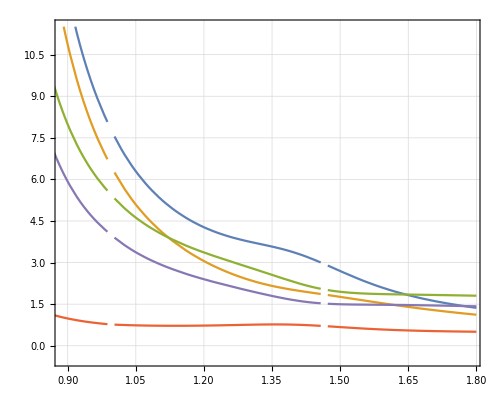

```mathematica
Plot[{Abs[Fvωπ[x^2]],Abs[FT1ωπ[x^2]],Abs[FT2ωπ[x^2]],Abs[FT3ωπ[x^2]],Abs[FT2p[x^2]]},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-.49,11.51}},FrameLabel->{{MaTeX["|F(s)|",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_V(s)","F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)","F_T2p"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.8,.85}]]
```

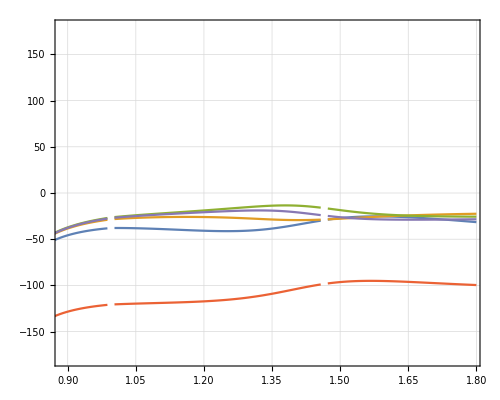

```mathematica
Plot[{Arg[Fvωπ[x^2]]*180/Pi,Arg[FT1ωπ[x^2]]*180/Pi,Arg[FT2ωπ[x^2]]*180/Pi,Arg[FT3ωπ[x^2]]*180/Pi,Arg[FT2p[x^2]]*180/Pi},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-180,180}},FrameLabel->{{MaTeX["\\delta",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_V(s)","F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.8,.85}]]
```

### ωK

```mathematica
ΔωK=Mω^2-MK^2;
ΣωK=Mω^2+MK^2;
```

```mathematica
σKπ[s_]:=1/s √((s-(MK+Mπ)^2)(s-(MK-Mπ)^2))HeavisideTheta[s-(MK+Mπ)^2];
σKη[s_]:=1/s √((s-(MK+Mη)^2)(s-(MK-Mη)^2))HeavisideTheta[s-(MK+Mη)^2];
```

```mathematica
σKρ[s_]:=1/s √((s-(MK+Mρ)^2)(s-(MK-Mρ)^2))HeavisideTheta[s-(MK+Mρ)^2];
```

```mathematica
σKsπ[s_]:=1/s √((s-(MKs+Mπ)^2)(s-(MKs-Mπ)^2))HeavisideTheta[s-(MKs+Mπ)^2];
```

```mathematica
ΓKs[s_]:=Γ0Ks s/MKs^2((σKπ[s]^3+σKη[s]^3)/(σKπ[MKs^2]^3+σKη[MKs^2]^3));
ΓKsp[s_]:=Γ0Ksp s/MKsp^2((σKπ[s]^3+σKη[s]^3)/(σKπ[MKsp^2]^3+σKη[MKsp^2]^3));
```

```mathematica
DKs[s_]:=1/(MKs^2-s-I MKs ΓKs[s]);
DKsp[s_]:=1/(MKsp^2-s-I MKsp ΓKsp[s]);
```

```mathematica
DK[s_]:=1/(MK^2-s);
```

```mathematica
ΓK1H[s_]:=Γ0K1H s/MK1H^2((σKρ[s]^3+σKsπ[s]^3)/(σKρ[MK1H^2]^3+σKsπ[MK1H^2]^3));
```

```mathematica
ΓK1L[s_]:=Γ0K1L s/MK1L^2((σKρ[s]^3+σKsπ[s]^3)/(σKρ[MK1L^2]^3+σKsπ[MK1L^2]^3));
```

```mathematica
DK1H[s_]:=1/(MK1H^2-s-I MK1H ΓK1H[s]);
DK1L[s_]:=1/(MK1L^2-s-I MK1L ΓK1L[s]);
```

```mathematica
FvωK[s_]:=((√2)/(FK Mω)(2 d3 fv+ds FV1)+(2 √2 fv)/(FK Mω)(d12 MK^2+d3(s+ΔωK))DKs[s]+(√2 FV1)/(FK Mω)(dm MK^2+dM Mω^2+ds s)DKsp[s])/.FFNValues2;
```

```mathematica
A1ωK[s_]:=I √2 1/(4 Mω FK)(-fv(ΔωK+s)-2 Gv (ΣωK-s)+2 √2 FA (λ0 MK^4+(Mω^2-s)(λp Mω^2-λpp s)-MK^2(λ0 Mω^2+λp Mω^2+λ0 s +λpp s))(cθ^2 DK1H[s]+sθ^2 DK1L[s]) )/.FFNValues2;
```

```mathematica
A2ωK[s_]:=I √2(-(Gv Mω)/FK DK[s]+(√2 FA Mω)/FK(λp+λpp)(cθ^2 DK1H[s]+sθ^2 DK1L[s]))/.FFNValues2;
```

```mathematica
A3ωK[s_]:=I √2((fv-2Gv)/(2FK Mω)-(Gv Mω)/FK DK[s]+(√2 FA)/(FK Mω)(λ0 MK^2+λpp Mω^2-λpp s)(cθ^2 DK1H[s]+sθ^2 DK1L[s]))/.FFNValues2;
```

```mathematica
FT1ωK[s_]:=((4 FVT)/(FK Mω MKs^2)(d12 MK^2+d3(ΔωK+MKs^2))DKs[s]-(4 FV1T)/(FK Mω MKsp^2)(dd Mω^2-(db+4df)MK^2-(da-db)MKsp^2)DKsp[s])/.FFNValues2;
```

```mathematica
FT2ωK[s_]:=(-(2FVT)/(FK Mω MKs^2)((d12 MK^2-d3(ΣωK-MKs^2))+(d12 MK^2(s+ΔωK)-d3(s ΣωK-ΔωK^2+MKs^2(2 Mω^2+s+ΔωK)))DKs[s])-2 FV1T/(FK Mω MKsp^2)((dd Mω^2+(db+4 df)MKs^2+(da-db)MKsp^2)(1+(s-ΣωK)DKsp[s])+2 Mω^2((db+dd+4df)MK^2+(da-db-dd)MKsp^2)DKsp[s]))/.FFNValues2;
```

```mathematica
FT3ωK[s_]:=(-(2 FVT)/(FK Mω MKs^2)((d12 MK^2-d3(ΣωK+MKs^2)) +(d12 MK^2(s+ΔωK-2 MKs^2)-d3(s ΣωK-ΔωK^2+MKs^2(s-ΣωK)))DKs[s])-2 FV1T/(FK Mω MKsp^2)((dd Mω^2+(db+4df)MK^2-(da-db)MKsp^2)(1+(s-ΣωK)DKsp[s])+2 MK^2((db+dd+4df)Mω^2-(da+4df)MKsp^2)DKsp[s]))/.FFNValues2;
```

```mathematica
FFωK={Fv->FvωK[s],A1->A1ωK[s],A2->A2ωK[s],A3->A3ωK[s],FT1->FT1ωK[s],FT2->FT2ωK[s],FT3->FT3ωK[s]};
```

#### Plots

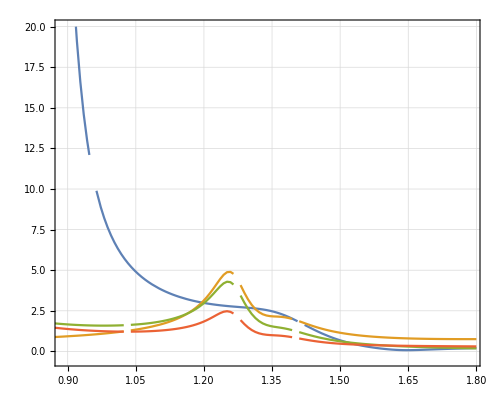

```mathematica
Plot[{Abs[FvωK[x^2]],Abs[A1ωK[x^2]],Abs[A2ωK[x^2]],Abs[A3ωK[x^2]]},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-.49,20}},FrameLabel->{{MaTeX["|F(s)|",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_V(s)","F_{A_1}(s)","F_{A_2}(s)","F_{A_3}(s)","F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.85,.72}]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"FFOmegaK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/FFOmegaK_1.pdf

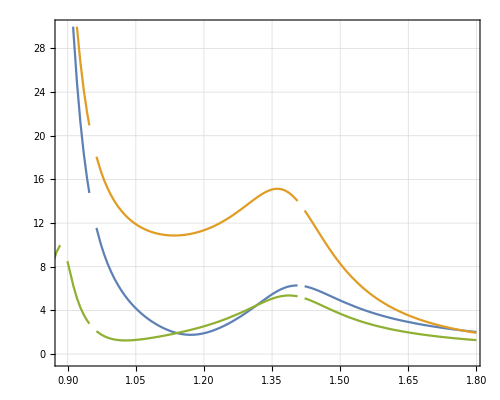

```mathematica
Plot[{Abs[FT1ωK[x^2]],Abs[FT2ωK[x^2]],Abs[FT3ωK[x^2]]},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-.49,30}},FrameLabel->{{MaTeX["|F(s)|",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_V(s)","F_{A_1}(s)","F_{A_2}(s)","F_{A_3}(s)","F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.85,.72}]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"FFOmegaK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/FFOmegaK_2.pdf

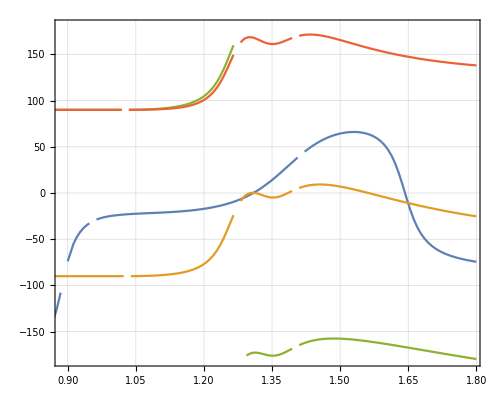

```mathematica
Plot[{Arg[FvωK[x^2]]*180/Pi,Arg[A1ωK[x^2]]*180/Pi,Arg[A2ωK[x^2]]*180/Pi,Arg[A3ωK[x^2]]*180/Pi},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-180,180}},FrameLabel->{{MaTeX["\\delta",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_V(s)","F_{A_1}(s)","F_{A_2}(s)","F_{A_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.2,.85}]]
```

### ρK

```mathematica
ΔρK=Mρ^2-MK^2;
ΣρK=Mρ^2+MK^2;
```

```mathematica
FvρK[s_]:=((√2)/(FK Mρ)(2 d3 fv+ds FV1)+(2 √2 fv)/(FK Mρ)(d12 MK^2+d3(s+ΔρK))DKs[s]+(√2 FV1)/(FK Mρ)(dm MK^2+dM Mρ^2+ds s)DKsp[s])/.FFNValues2;
```

```mathematica
A1ρK[s_]:=I √2 1/(4 Mρ FK)(-fv(ΔρK+s)-2 Gv (ΣρK-s)+2 √2 FA (λ0 MK^4+(Mρ^2-s)(λp Mρ^2-λpp s)-MK^2(λ0 Mρ^2+λp Mρ^2+λ0 s +λpp s))(cθ^2 DK1H[s]+sθ^2 DK1L[s]) )/.FFNValues2;
```

```mathematica
A2ρK[s_]:=I √2(-(Gv Mρ)/FK DK[s]+(√2 FA Mρ)/FK(λp+λpp)(cθ^2 DK1H[s]+sθ^2 DK1L[s]))/.FFNValues2;
```

```mathematica
A3ρK[s_]:=I √2((fv-2Gv)/(2FK Mρ)-(Gv Mρ)/FK DK[s]+(√2 FA)/(FK Mρ)(λ0 MK^2+λpp Mρ^2-λpp s)(cθ^2 DK1H[s]+sθ^2 DK1L[s]))/.FFNValues2;
```

```mathematica
FT1ρK[s_]:=((4 FVT)/(FK Mρ MKs^2)(d12 MK^2+d3(ΔρK+MKs^2))DKs[s]-(4 FV1T)/(FK Mρ MKsp^2)(dd Mρ^2-(db+4df)MK^2-(da-db)MKsp^2)DKsp[s])/.FFNValues2;
```

```mathematica
FT2ρK[s_]:=(-(2FVT)/(FK Mρ MKs^2)((d12 MK^2-d3(ΣρK-MKs^2))+(d12 MK^2(s+ΔρK)-d3(s ΣρK-ΔρK^2+MKs^2(2 Mρ^2+s+ΔρK)))DKs[s])-2 FV1T/(FK Mρ MKsp^2)((dd Mρ^2+(db+4 df)MKs^2+(da-db)MKsp^2)(1+(s-ΣρK)DKsp[s])+2 Mρ^2((db+dd+4df)MK^2+(da-db-dd)MKsp^2)DKsp[s]))/.FFNValues2;
```

```mathematica
FT3ρK[s_]:=(-(2 FVT)/(FK Mρ MKs^2)((d12 MK^2-d3(ΣρK+MKs^2)) +(d12 MK^2(s+ΔρK-2 MKs^2)-d3(s ΣρK-ΔρK^2+MKs^2(s-ΣρK)))DKs[s])-2 FV1T/(FK Mρ MKsp^2)((dd Mρ^2+(db+4df)MK^2-(da-db)MKsp^2)(1+(s-ΣρK)DKsp[s])+2 MK^2((db+dd+4df)Mρ^2-(da+4df)MKsp^2)DKsp[s]))/.FFNValues2;
```

```mathematica
FFρK={Fv->FvρK[s],A1->A1ρK[s],A2->A2ρK[s],A3->A3ρK[s],FT1->FT1ρK[s],FT2->FT2ρK[s],FT3->FT3ρK[s]};
```

#### Plots

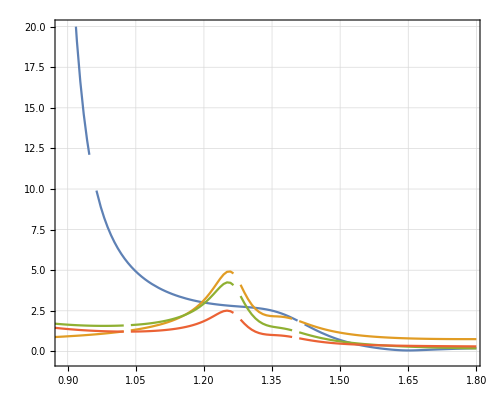

```mathematica
Plot[{Abs[FvρK[x^2]],Abs[A1ρK[x^2]],Abs[A2ρK[x^2]],Abs[A3ρK[x^2]]},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-.49,20}},FrameLabel->{{MaTeX["|F(s)|",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_V(s)","F_{A_1}(s)","F_{A_2}(s)","F_{A_3}(s)","F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.85,.72}]]
```

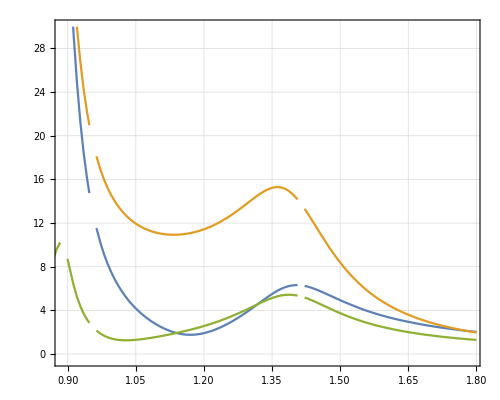

```mathematica
Plot[{Abs[FT1ρK[x^2]],Abs[FT2ρK[x^2]],Abs[FT3ρK[x^2]]},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-.49,30}},FrameLabel->{{MaTeX["|F(s)|",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.85,.72}]]
```

### (K̄)^*π

```mathematica
ΔKsπ=MKs^2-Mπ^2;
ΣKsπ=MKs^2+Mπ^2;
```

```mathematica
FvKsπ[s_]:=((√2)/(F MKs)(2 d3 fv+ds FV1)+(2 √2 fv)/(F MKs)(d12 Mπ^2+d3(s+ΔKsπ))DKs[s]+(√2 FV1)/(F MKs)(dm Mπ^2+dM MKs^2+ds s)DKsp[s])/.FFNValues2;
```

```mathematica
A1Ksπ[s_]:=I √2 1/(4 MKs F)(-fv(ΔKsπ+s)-2 Gv (ΣKsπ-s)+2 √2 FA (λ0 Mπ^4+(MKs^2-s)(λp MKs^2-λpp s)-Mπ^2(λ0 MKs^2+λp MKs^2+λ0 s +λpp s))(cθ^2 DK1H[s]+sθ^2 DK1L[s]) )/.FFNValues2;
```

```mathematica
A2Ksπ[s_]:=I √2(-(Gv MKs)/F DK[s]+(√2 FA MKs)/F(λp+λpp)(cθ^2 DK1H[s]+sθ^2 DK1L[s]))/.FFNValues2;
```

```mathematica
A3Ksπ[s_]:=I √2((fv-2Gv)/(2F MKs)-(Gv MKs)/F DK[s]+(√2 FA)/(F MKs)(λ0 Mπ^2+λpp MKs^2-λpp s)(cθ^2 DK1H[s]+sθ^2 DK1L[s]))/.FFNValues2;
```

```mathematica
FT1Ksπ[s_]:=((4 FVT)/(F MKs MKs^2)(d12 Mπ^2+d3(ΔKsπ+MKs^2))DKs[s]-(4 FV1T)/(F MKs MKsp^2)(dd MKs^2-(db+4df)Mπ^2-(da-db)MKsp^2)DKsp[s])/.FFNValues2;
```

```mathematica
FT2Ksπ[s_]:=(-(2FVT)/(F MKs MKs^2)((d12 Mπ^2-d3(ΣKsπ-MKs^2))+(d12 Mπ^2(s+ΔKsπ)-d3(s ΣKsπ-ΔKsπ^2+MKs^2(2 MKs^2+s+ΔKsπ)))DKs[s])-2 FV1T/(F MKs MKsp^2)((dd MKs^2+(db+4 df)MKs^2+(da-db)MKsp^2)(1+(s-ΣKsπ)DKsp[s])+2 MKs^2((db+dd+4df)Mπ^2+(da-db-dd)MKsp^2)DKsp[s]))/.FFNValues2;
```

```mathematica
FT3Ksπ[s_]:=(-(2 FVT)/(F MKs MKs^2)((d12 Mπ^2-d3(ΣKsπ+MKs^2)) +(d12 Mπ^2(s+ΔKsπ-2 MKs^2)-d3(s ΣKsπ-ΔKsπ^2+MKs^2(s-ΣKsπ)))DKs[s])-2 FV1T/(F MKs MKsp^2)((dd MKs^2+(db+4df)Mπ^2-(da-db)MKsp^2)(1+(s-ΣKsπ)DKsp[s])+2 Mπ^2((db+dd+4df)MKs^2-(da+4df)MKsp^2)DKsp[s]))/.FFNValues2;
```

```mathematica
FFKsπ={Fv->FvKsπ[s],A1->A1Ksπ[s],A2->A2Ksπ[s],A3->A3Ksπ[s],FT1->FT1Ksπ[s],FT2->FT2Ksπ[s],FT3->FT3Ksπ[s]};
```

#### Plots

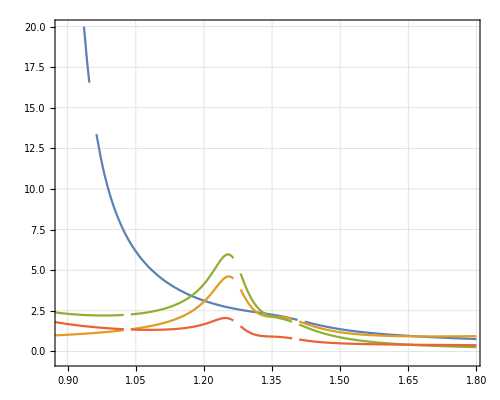

```mathematica
Plot[{Abs[FvKsπ[x^2]],Abs[A1Ksπ[x^2]],Abs[A2Ksπ[x^2]],Abs[A3Ksπ[x^2]]},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-.49,20}},FrameLabel->{{MaTeX["|F(s)|",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_V(s)","F_{A_1}(s)","F_{A_2}(s)","F_{A_3}(s)","F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.85,.72}]]
```

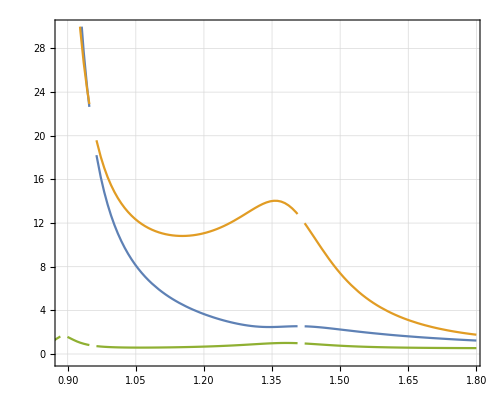

```mathematica
Plot[{Abs[FT1Ksπ[x^2]],Abs[FT2Ksπ[x^2]],Abs[FT3Ksπ[x^2]]},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-.49,30}},FrameLabel->{{MaTeX["|F(s)|",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.85,.72}]]
```

### (K̄)^*K

```mathematica
ΔKsK=MKs^2-MK^2;
ΣKsK=MKs^2+MK^2;
```

```mathematica
σπρ[s_]:=1/2 √((s-(Mπ+Mρ)^2)(s-(Mπ-Mρ)^2))HeavisideTheta[s-(Mπ+Mρ)^2];
σKKs[s_]:=1/2 √((s-(MK+MKs)^2)(s-(MK-MKs)^2))HeavisideTheta[s-(MK+MKs)^2];
```

```mathematica
Γa1[s_]:=Γa10 s/Ma1^2((σπρ[s]^3+1/2 σKKs[s]^3)/(σπρ[Ma1^2]^3+1/2 σKKs[Ma1^2]^3))
```

```mathematica
Da1[s_]:=1/(Ma1^2-s-I Ma1 Γa1[s]);
```

```mathematica
Dπ[s_]:=1/(Mπ^2-s);
```

```mathematica
FvKsK[s_]:=((2 √2)/(FK MKs)(2 d3 fv+ds FV1)+(4 √2 fv)/(FK MKs)(d12 MK^2+d3(s+ΔKsK))Dρ[s]+(2 √2 FV1)/(FK MKs)(dm MK^2 + dM MKs^2+ ds s)Dρp[s])/.FFNValues2;
```

```mathematica
A1KsK[s_]:=-1/(2 √2 MKs FK)(fv (MK^2-MKs^2-s)-2Gv (MK^2+MKs^2-s)+2 √2 FA (λ0 MK^4+(MKs^2-s)(λp MKs^2-λpp s)-MK^2(λ0 MKs^2+λp MKs^2+λ0 s +λpp s)) Da1[s])/.FFNValues2;
```

```mathematica
A2KsK[s_]:=(√2 Gv MKs)/FK Dπ[s]-2(FA MKs)/FK(λp+λpp)Da1[s]/.FFNValues2;
```

```mathematica
A3KsK[s_]:=(-fv+2Gv)/(√2 FK MKs)+(√2 Gv MKs)/FK Dπ[s]-(2FA)/(FK MKs)(λ0 MK^2+λpp MK^2-λpp s)Da1[s]/.FFNValues2;
```

```mathematica
FT1KsK[s_]:=((4 FVT)/(FK MKs Mρ^2)(d12 MK^2+d3(ΔKsK+Mρ^2))Dρ[s]-(4 FV1T)/(FK MKs Mρp^2)(dd MKs^2-(db+4df)MK^2-(da-db)Mρp^2)Dρp[s])/.FFNValues;
```

```mathematica
FT2KsK[s_]:=(-(2FVT)/(FK MKs Mρ^2)((d12 MK^2-d3(ΣKsK-Mρ^2))+(d12 MK^2(s+ΔKsK)-d3(s ΣKsK-ΔKsK^2+Mρ^2(2 MKs^2+s+ΔKsK)))Dρ[s])-2 FV1T/(FK MKs Mρp^2)((dd MKs^2+(db+4 df)MK^2+(da-db)Mρp^2)(1+(s-ΣKsK)Dρp[s])+2 MKs^2((db+dd+4df)MK^2+(da-db-dd)Mρp^2)Dρp[s]))/.FFNValues;
```

```mathematica
FT3KsK[s_]:=(-(2 FVT)/(FK MKs Mρ^2)((d12 MK^2-d3(ΣKsK+Mρ^2)) +(d12 MK^2(s+ΔKsK-2 Mρ^2)-d3(s ΣKsK-ΔKsK^2+Mρ^2(s-ΣKsK)))Dρ[s])-2 FV1T/(FK MKs Mρp^2)((dd MKs^2+(db+4df)MK^2-(da-db)Mρp^2)(1+(s-ΣKsK)Dρp[s])+2 MK^2((db+dd+4df)MKs^2-(da+4df)Mρp^2)Dρp[s]))/.FFNValues;
```

```mathematica
FFKsK={Fv->FvKsK[s],A1->A1KsK[s],A2->A2KsK[s],A3->A3KsK[s],FT1->FT1KsK[s],FT2->FT2KsK[s],FT3->FT3KsK[s]};
```

#### Plots

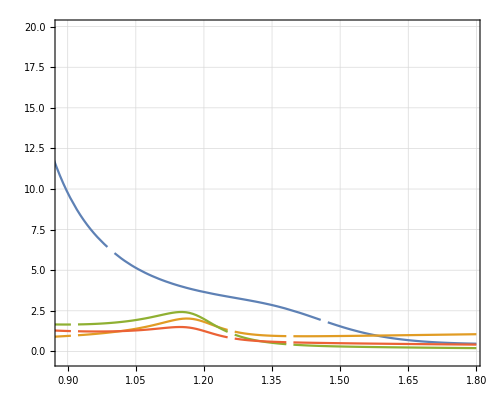

```mathematica
Plot[{Abs[FvKsK[x^2]],Abs[A1KsK[x^2]],Abs[A2KsK[x^2]],Abs[A3KsK[x^2]]},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-.49,20}},FrameLabel->{{MaTeX["|F(s)|",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_V(s)","F_{A_1}(s)","F_{A_2}(s)","F_{A_3}(s)","F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.85,.72}]]
```

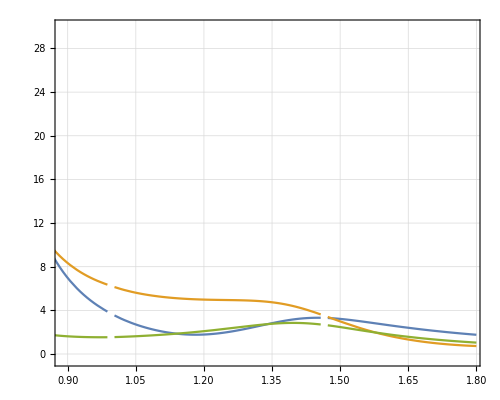

```mathematica
Plot[{Abs[FT1KsK[x^2]],Abs[FT2KsK[x^2]],Abs[FT3KsK[x^2]]},{x,.8,1.8},PlotPoints->3,PlotRange->{{.89,1.79},{-.49,30}},FrameLabel->{{MaTeX["|F(s)|",Magnification->1.5]," "},{MaTeX["\\sqrt{s}[\\textrm{GeV}]",Magnification->1.5],MaTeX["",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"F_{T_1}(s)","F_{T_2}(s)","F_{T_3}(s)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.85,.72}]]
```

## Amplitudes

### General expressions

```mathematica
SQRT[M1_,M2_]:=FermionSpinSum[DoPolarizationSums[M1 M2,pV]]//Calc;
```

```mathematica
HV[μ_]:=I Fv LC[μ,ν,ρ,σ]FV[pp,ρ]FV[pV,σ]Conjugate[PolarizationVector[pV,ν]]//Contract;
```

```mathematica
HA[μ_]:=(A1 MetricTensor[μ,ν]+A2 FV[pp,μ]FV[pp,ν]+A3 FV[pV,μ]FV[pp,ν])Conjugate[PolarizationVector[pV,ν]]//Contract;
```

```mathematica
HT[μ_,ν_]:= LC[μ,ν,ρ,σ]*(FT1 FV[pp,ρ]FV[pV,σ]Conjugate[PolarizationVector[pV,a]]FV[pp,a]-FT2 Conjugate[PolarizationVector[pV,ρ]]FV[pp,σ]-FT3 Conjugate[PolarizationVector[pV,ρ]] FV[pV,σ])//Contract;
```

```mathematica
L[μ_]:=SpinorUBar[pν,0].GA[μ].(1-GA[5]).SpinorU[pτ,mτ];
```

```mathematica
LL[μ_,ν_]:=I/2 SpinorUBar[pν,0].(GA[μ,ν]-GA[ν,μ]).(1+GA[5]).SpinorU[pτ,mτ];
```

```mathematica
MTot=-I(GF Vckm)/(√2)(L[μ]*HV[μ]-(1-2ϵR) L[μ]*HA[μ]+2ϵT LL[μ,ν]*HT[μ,ν])//Contract//Simplify;
```

```mathematica
MTot//TraditionalForm
```

1/(√2)GF Vckm (-ⅈ A1 (2 ϵR-1) (φ(OverBar[pν])).(γ̄·(ε̄)^*(pV)).(1-(γ̄)^5).(φ(OverBar[pτ],mτ))+ⅈ A2 (OverBar[pp]·(ε̄)^*(pV)) (φ(OverBar[pν])).(γ̄·OverBar[pp]).(1-(γ̄)^5).(φ(OverBar[pτ],mτ))-2 ⅈ A2 ϵR (OverBar[pp]·(ε̄)^*(pV)) (φ(OverBar[pν])).(γ̄·OverBar[pp]).(1-(γ̄)^5).(φ(OverBar[pτ],mτ))+ⅈ A3 (OverBar[pp]·(ε̄)^*(pV)) (φ(OverBar[pν])).(γ̄·OverBar[pV]).(1-(γ̄)^5).(φ(OverBar[pτ],mτ))-2 ⅈ A3 ϵR (OverBar[pp]·(ε̄)^*(pV)) (φ(OverBar[pν])).(γ̄·OverBar[pV]).(1-(γ̄)^5).(φ(OverBar[pτ],mτ))+ϵT (φ(OverBar[pν])).((γ̄)^μ.(γ̄)^ν-(γ̄)^ν.(γ̄)^μ).((γ̄)^5+1).(φ(OverBar[pτ],mτ)) (FT1 (OverBar[pp]·(ε̄)^*(pV)) (ϵ̄)^(μν OverBar[pp]OverBar[pV])+FT2 (ϵ̄)^(μν OverBar[pp](ε̄)^*(pV))+FT3 (ϵ̄)^(μν OverBar[pV](ε̄)^*(pV)))+Fv (ϵ̄)^(μ OverBar[pp]OverBar[pV](ε̄)^*(pV)) (φ(OverBar[pν])).(γ̄)^μ.(1-(γ̄)^5).(φ(OverBar[pτ],mτ)))

```mathematica
MTotC=ComplexConjugate[MTot]/.(#->Conjugate[#]&/@{Fv,A1,A2,A3,FT1,FT2,FT3});
```

```mathematica
MTot2=SQRT[MTot,MTotC];
```

```mathematica
d2Γ=1/(2 Pi)^3 1/(32 mτ^3)SEW 1/2 MTot2/.Kin3B[pτ,pν,pp,pV,mτ,0,mp,mV];
```

```mathematica
d2Γθ=Det[JJ]*d2Γ/.{t->tp}/.Cos[θ]->x;
```

```mathematica
Coefθ=CoefficientList[d2Γθ,x]//Simplify//PowerExpand;
```

```mathematica
dΓ=Integrate[d2Γ,{t,tmin[mτ,0,mp,mV],tmax[mτ,0,mp,mV]}];
```

```mathematica
AFB=(3Coefθ[[2]])/(6Coefθ[[1]]+2Coefθ[[3]])//Simplify;
```

```mathematica
dΓT[saux_,ϵTaux_,ϵRaux_,FF_,NV_]:=dΓ/.FF/.{λ->λp}/.{s->saux,ϵT->ϵTaux,ϵR->ϵRaux}/.NV;
d2ΓT[saux_,taux_,ϵTaux_,ϵRaux_,FF_,NV_]:=d2Γ/.FF/.{λ->λp}/.{s->saux,t->taux,ϵT->ϵTaux,ϵR->ϵRaux}/.NV;
d2ΓCθT[saux_,xaux_,ϵTaux_,ϵRaux_,FF_,NV_]:=d2Γθ/.FF/.{λ->λp}/.{s->saux,x->xaux,ϵT->ϵTaux,ϵR->ϵRaux}/.NV;
BRT[ϵTaux_,ϵRaux_,FF_,NV_]:=ττ*NIntegrate[dΓT[s,ϵTaux,ϵRaux,FF,NV],{s,(mp+mV)^2/.NV,mτ^2/.NV},Method->"AdaptiveMonteCarlo",WorkingPrecision->10,PrecisionGoal->4,MaxRecursion->50];
ΓT[ϵTaux_,ϵRaux_,FF_,NV_]:=NIntegrate[dΓT[s,ϵTaux,ϵRaux,FF,NV],{s,(mp+mV)^2/.NV,mτ^2/.NV},Method->"AdaptiveMonteCarlo",WorkingPrecision->10,PrecisionGoal->4,MaxRecursion->50];
AFBT[saux_,ϵTaux_,ϵRaux_,FF_,NV_]:=AFB/.FF/.{λ->λp}/.{s->saux,ϵT->ϵTaux,ϵR->ϵRaux}/.NV;;
```

```mathematica
NNT[saux_,ϵTaux_,ϵRaux_,FF_,NV_]:=dΓT[saux,ϵTaux,ϵRaux,FF,NV]/ΓT[ϵTaux,ϵRaux,FF,NV];
```

```mathematica
ΔtT[saux_,taux_,ϵTaux_,ϵRaux_,FF_,NV_]:=1-d2ΓT[saux,taux,ϵTaux,ϵRaux,FF,NV]/d2ΓT[saux,taux,0.0,0.0,FF,NV];
```

```mathematica
ΔtθT[saux_,xaux_,ϵTaux_,ϵRaux_,FF_,NV_]:=1-d2ΓCθT[saux,xaux,ϵTaux,ϵRaux,FF,NV]/d2ΓCθT[saux,xaux,0.0,0.0,FF,NV] ;
```

Definition for functions dedicated to ωπ channel

```mathematica
dΓsωπ[saux_,ϵTaux_]:=dΓT[saux,ϵTaux,0.0,FFωπ,NVALUESωπ];
```

```mathematica
d2Γωπ[saux_,taux_,ϵTaux_]:=d2ΓT[saux,taux,ϵTaux,0.0,FFωπ,NVALUESωπ]
```

```mathematica
d2ΓωπdCθ[saux_,xaux_,ϵTaux_]:=d2ΓCθT[saux,xaux,ϵTaux,0.0,FFωπ,NVALUESωπ];
```

```mathematica
BRωπT[ϵTaux_]:=BRT[ϵTaux,0.0,FFωπ,NVALUESωπ];
```

```mathematica
AFBωπT[saux_,ϵTaux_]:=AFBT[saux,ϵTaux,0.0,FFωπ,NVALUESωπ]
```

```mathematica
BRωπT[0.0]
```

0.0203875

```mathematica
d2Γωπ[1.5^2,.4,0]
```

2.99831×10^-14+1.83192×10^-30 ⅈ

Definition of functions dedicated to ωK channel

```mathematica
dΓsωK[saux_,ϵTaux_,ϵRaux_]:=dΓT[saux,ϵTaux,ϵRaux,FFωK,NVALUESωK];
```

```mathematica
d2ΓωK[saux_,taux_,ϵTaux_,ϵRaux_]:=d2ΓT[saux,taux,ϵTaux,ϵRaux,FFωK,NVALUESωK]
```

```mathematica
d2ΓωKdCθ[saux_,xaux_,ϵTaux_,ϵRaux_]:=d2ΓCθT[saux,xaux,ϵTaux,ϵRaux,FFωK,NVALUESωK];
```

```mathematica
BRωKT[ϵTaux_,ϵRaux_]:=BRT[ϵTaux,ϵRaux,FFωK,NVALUESωK];
```

```mathematica
AFBωKT[saux_,ϵTaux_,ϵRaux_]:=AFBT[saux,ϵTaux,ϵRaux,FFωK,NVALUESωK]
```

```mathematica
BRωKT[0.0,0.0]
```

0.000408969

```mathematica
NNT[1.4^2,0.0,0.012,FFωK,NVALUESωK]
```

1.58131+0. ⅈ

### Partial Amplitudes and total decay rate

```mathematica
M1=-I(GF Vckm)/(√2)L[μ]*HV[μ]//Contract//EpsContract//EpsEvaluate;
M2=-I(GF Vckm)/(√2)L[μ]*HA[μ]//Contract//EpsContract//EpsEvaluate;
M3=-I(GF Vckm)/(√2) LL[μ,ν]*HT[μ,ν]//Contract//EpsContract//EpsEvaluate;
```

```mathematica
M1C=ComplexConjugate[M1]/.(#->Conjugate[#]&/@{Fv,A1,A2,A3,FT1,FT2,FT3});
M2C=ComplexConjugate[M2]/.(#->Conjugate[#]&/@{Fv,A1,A2,A3,FT1,FT2,FT3});
M3C=ComplexConjugate[M3]/.(#->Conjugate[#]&/@{Fv,A1,A2,A3,FT1,FT2,FT3});
```

```mathematica
M11=SQRT[M1 ,M1C];
M22=SQRT[M2 ,M2C];
M33=SQRT[M3 ,M3C];
```

```mathematica
M12=SQRT[M1,M2C]+SQRT[M2,M1C]//Simplify;
M13=SQRT[M1,M3C]+SQRT[M3,M1C]//Simplify;
M23=SQRT[M2,M3C]+SQRT[M3,M2C]//Simplify;
```

```mathematica
Results1=(Integrate[1/(2 Pi)^3 SEW/(32 mτ^3)1/2(#/.Kin3B[pτ,pν,pp,pV,mτ,0,mp,mV]),{t,tmin[mτ,0,mp,mV],tmax[mτ,0,mp,mV]}]//Simplify)&/@{M11,M22,M33};
```

```mathematica
Results2=(Integrate[1/(2 Pi)^3 SEW/(32 mτ^3)1/2(#/.Kin3B[pτ,pν,pp,pV,mτ,0,mp,mV]),{t,tmin[mτ,0,mp,mV],tmax[mτ,0,mp,mV]}]//FullSimplify)&/@{M12,M13,M23};
```

```mathematica
ll=(384 Pi^2 s)/(GF^2 SEW mτ^3 Vckm^2)Results2[[3]]/.{mV^2-mp^2->ΔVp,mp^2-mV^2->-ΔVp,mp^2+mV^2->ΣVp,(mτ^2-s)-> √λ[mτ^2,0,s],mp^4+(mV^2-s)^2-2 mp^2 (mV^2+s)->λ[s,mV^2,mp^2]}//FullSimplify
```

1/(16 mV^2 mτ^5 π s)3 √λ[mτ^2,0,s] √(λ[mτ^2,0,s] λ[s,mp^2,mV^2]) (2 (-2 A1 (mp^4-5 mV^4+mp^2 (4 mV^2-2 s)+4 mV^2 s+s^2)+(A2-A3) ((mp-mV)^2-s) ((mp+mV)^2-s) (s-ΣVp)) Conjugate[FT2]-4 mV^2 Conjugate[FT3] (6 A1 (s+ΔVp)+(-A2+A3) λ[s,mV^2,mp^2])-2 Conjugate[A1] (2 FT2 (mp^4-5 mV^4+mp^2 (4 mV^2-2 s)+4 mV^2 s+s^2)+12 FT3 mV^2 (s+ΔVp)+FT1 (s+ΔVp) λ[s,mV^2,mp^2])+λ[s,mV^2,mp^2] (2 (2 FT3 mV^2+FT2 (s-ΣVp)) (Conjugate[A2]-Conjugate[A3])-2 A1 (s+ΔVp) Conjugate[FT1]+(FT1 Conjugate[A2]-FT1 Conjugate[A3]+(A2-A3) Conjugate[FT1]) λ[s,mV^2,mp^2]))

```mathematica
(Coefficient[ll, Conjugate[FT3]]//Simplify)/.{mV^2-mp^2->ΔVp,mp^2-mV^2->-ΔVp,(mp^2+mV^2)->ΣVp,(mτ^2-s)-> √λ[mτ^2,0,s],mp^4+(mV^2-s)^2-2 mp^2 (mV^2+s)->λ[s,mV^2,mp^2]}//FullSimplify//TraditionalForm
```

-(3 √(λ(mτ^2,0,s)) √(λ(mτ^2,0,s) λ(s,mp^2,mV^2)) ((A3-A2) λ(s,mV^2,mp^2)+6 A1 (ΔVp+s)))/(4 π mτ^5 s)

```mathematica
d2Γsim=1/(2Pi)^3 1/(32 mτ^3)SEW/2(M11+2ϵT(M13))/.Kin3B[pτ,pν,pp,pV,mτ,0,mp,mV]//Simplify
```

-1/(512 mτ^3 π^3)GF^2 SEW Vckm^2 (-8 Fv mτ (mp^4+(mV^2-s) t-mp^2 (mV^2-2 mτ^2+s+t)) ϵT Conjugate[FT2]+8 Fv mτ (mp^4+mV^2 (mτ^2-s+t)+s (-mτ^2+s+t)-mp^2 (mV^2-mτ^2+2 s+t)) ϵT Conjugate[FT3]+(Fv (mV^4 (-mτ^2+s)+mp^4 (mτ^2+s)+2 mp^2 (mτ^2+s) (mτ^2-s-t)+2 mV^2 (mτ^2-s) (s+t)+s (s^2+2 s t+2 t^2-mτ^2 (s+2 t)))-8 mτ (FT2 (mp^4+(mV^2-s) t-mp^2 (mV^2-2 mτ^2+s+t))-FT3 (mp^4+mV^2 (mτ^2-s+t)+s (-mτ^2+s+t)-mp^2 (mV^2-mτ^2+2 s+t))) ϵT) Conjugate[Fv])

```mathematica
d2ΓsimdCθωπ[saux_,Cθ_,ϵTaux_]:=(Det[JJ]*d2Γsim/.{t->tp}//Simplify)/.{s-> saux,Cos[θ]->Cθ,ϵT->ϵTaux}/.{Fv->Fvωπ[saux],A1->0,A2->0,A3->0,FT1->FT1ωπ[saux],FT2->FT2ωπ[saux],FT3->FT3ωπ[saux]}/.NVALUES;
```

```mathematica
Det[JJ]*d2Γsim/.{t->tp}//Expand;
```

```mathematica
ll=CoefficientList[%,Cos[θ]]//Simplify;
```

```mathematica
AFBSim=(3ll[[2]])/(6ll[[1]]+2ll[[3]])//Simplify;
```

```mathematica
AFBωπ[saux_,ϵTaux_]:=AFBSim/.{λ->λp}/.FFωπ/.{s->saux,ϵT->ϵTaux}/.NVALUESωπ;
```

```mathematica
dΓsim=Integrate[d2Γsim,{t,tmin[mτ,0,mp,mV],tmax[mτ,0,mp,mV]}]//FullSimplify
```

-1/(3072 mτ^3 π^3 s^2)GF^2 SEW Vckm^2 √(λ[mτ^2,0,s] λ[s,mp^2,mV^2]) (-3 (mτ^2-s) (mp^4+(mV^2-s)^2-2 mp^2 (mV^2+s)) (-8 Fv mτ ϵT Conjugate[FT2]+8 Fv mτ ϵT Conjugate[FT3]+(Fv (mτ^2+s)+8 (-FT2+FT3) mτ ϵT) Conjugate[Fv])+Fv Conjugate[Fv] λ[mτ^2,0,s] λ[s,mp^2,mV^2])

```mathematica
dΓsimS[saux_,ϵTaux_]:=dΓsim/.{λ->λp}/.FFωπ/.{s->saux,ϵT->ϵTaux}/.NVALUESωπ
```

```mathematica
Γωπ[ϵTaux_]:=NIntegrate[dΓsimS[x,ϵTaux],{x,(mp+mV)^2/.NVALUESωπ,mτ^2/.NVALUESωπ},Method->"AdaptiveMonteCarlo",WorkingPrecision->10,PrecisionGoal->4];
```

```mathematica
ττ*Γωπ[0]
```

0.0203888

```mathematica
FR1=ττ*NIntegrate[#/.λ->λp/.{s->saux}/.{Fv->FvωK[saux],A1->A1ωK[saux],A2->A2ωK[saux],A3->A3ωK[saux],FT1->FT1ωK[saux],FT2->FT2ωK[saux],FT3->FT3ωK[saux]}/.NVALUESωK,{saux,(mp+mV)^2/.NVALUESωK,mτ^2/.NVALUESωK},Method->"AdaptiveQuasiMonteCarlo",WorkingPrecision->8,PrecisionGoal->5,MaxRecursion->50]&/@Results1
```

{0.0000228455,0.000386108,0.0170221}

```mathematica
FR2=ττ*NIntegrate[#/.λ->λp/.{s->saux}/.{Fv->FvωK[saux],A1->A1ωK[saux],A2->A2ωK[saux],A3->A3ωK[saux],FT1->FT1ωK[saux],FT2->FT2ωK[saux],FT3->FT3ωK[saux]}/.NVALUESωK,{saux,(mp+mV)^2/.NVALUESωK,mτ^2/.NVALUESωK},Method->"AdaptiveQuasiMonteCarlo",WorkingPrecision->8,PrecisionGoal->5,MaxRecursion->50]&/@Results2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 51 recursive bisections in saux near {saux} = {1.}. NIntegrate obtained 0 and 0 for the integral and error estimates.

{0.,-0.000564764,-0.00336624}

```mathematica
FFR[FF_,NV_]:=ττ*NIntegrate[#/.FF/.λ->λp/.{s->saux}/.NV,{saux,(mp+mV)^2/.NV,mτ^2/.NV},Method->"AdaptiveQuasiMonteCarlo",WorkingPrecision->8,PrecisionGoal->5,MaxRecursion->50]&/@Join[Results1,Results2]
```

## Plots

### τ^-→ ω π^-(ν̄)_τ

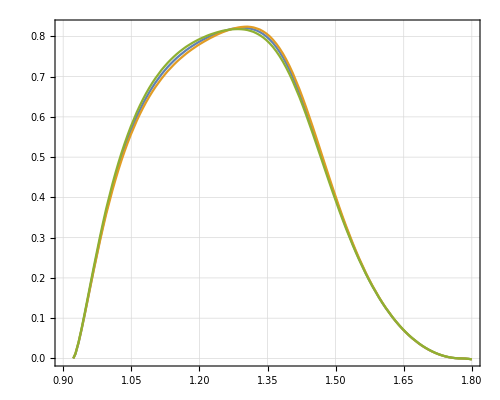

```mathematica
Plot[{NNT[x^2,0.0,0.0,FFωπ,NVALUESωπ],NNT[x^2,0.015,0.0,FFωπ,NVALUESωπ],NNT[x^2,-0.015,0.0,FFωπ,NVALUESωπ]},{x,.9,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}\\frac{d\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\omega\\pi^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=0","\\hat{\\epsilon}_T=0.015","\\hat{\\epsilon}_T=-0.015"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.8,.85}],PlotPoints->3]
```

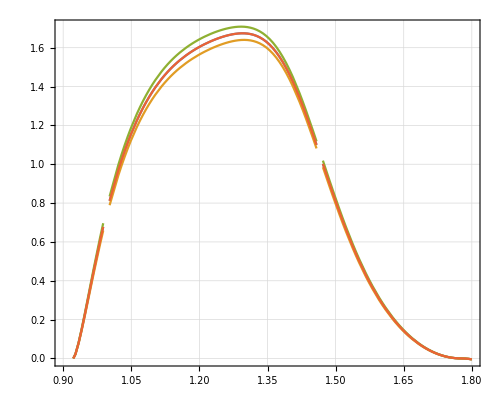

```mathematica
Plot[{100*ττ*dΓsimS[x^2,0.0],100*ττ*dΓsimS[x^2,5 10^-3],100*ττ*dΓsimS[x^2,-5 10^-3],100*ττ dΓsωπ[x^2,0.0]},{x,.9,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d\\Gamma}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\omega\\pi^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=0","\\hat{\\epsilon}_T=0.005","\\hat{\\epsilon}_T=-0.005","\\hat{\\epsilon}_T=0 (sim)"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.8,.85}],PlotPoints->3]
```

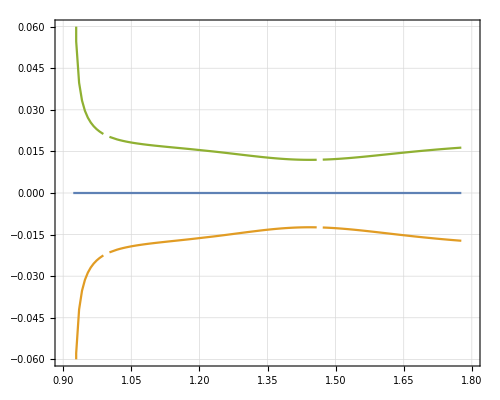

```mathematica
Plot[{AFBωπ[x^2,0],AFBωπ[x^2,0.005],AFBωπ[x^2,-0.005]},{x,mp+mV/.NVALUESωπ,mτ/.NVALUESωπ},FrameLabel->{{MaTeX["\\textrm{A}_{\\textrm{FB}}(s)",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\omega\\pi^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\epsilon_T=0","\\epsilon_T=0.005","\\epsilon_T=-0.005"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.8,.25}],PlotRange->{{.9,1.8},{-.06,.06}},PlotPoints->3]
```

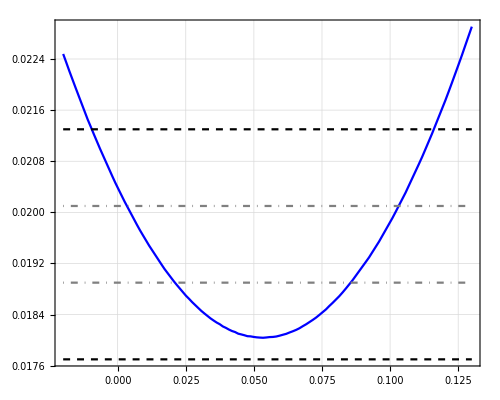

```mathematica
Plot[{BRωπT[ϵT],(1.95+3 0.06)/100,(1.95-3 0.06)/100,(1.95+0.06)/100,(1.95-0.06)/100},{ϵT,-.02,.13},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\textrm{BR}(\\tau^-\\to \\omega\\pi^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3]
```

```mathematica
Plot[{BRωπT[ϵT]/BRωπT[0.0]-1,(1.95+3 0.06)/2.1-1,(1.95-3 0.06)/2.1-1,(1.95+0.06)/2.1-1,(1.95-0.06)/2.1-1},{ϵT,-.02,.13},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\Delta(\\tau^-\\to \\omega\\pi^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3]
```

```mathematica
min=0.0;
max=0.023;
ramp=ColorData["Rainbow"];
plotCF=ramp[Rescale[Last@{##},{min,max}]]&;
legendCF=ramp[Rescale[#,{min,max}]]&;
legend=Placed[BarLegend[{legendCF,{min,max}}],After];
```

```mathematica
Plt1=DensityPlot[Piecewise[{{ττ*Abs[d2Γωπ[saux,taux,0.0]],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωπ]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωπ]}},Null],{saux,(mV+mp)^2/.NVALUESωπ,mτ^2/.NVALUESωπ},{taux,(mp)^2/.NVALUESωπ,(mτ-mV)^2/.NVALUESωπ},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["t[\\textrm{GeV}]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Plt2=DensityPlot[Piecewise[{{ττ*d2Γωπ[saux,taux,-0.014],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωπ]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωπ]}},Null],{saux,(mV+mp)^2/.NVALUESωπ,mτ^2/.NVALUESωπ},{taux,(mp)^2/.NVALUESωπ,(mτ-mV)^2/.NVALUESωπ},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->plotCF,PlotLegends->legend,PlotPoints->20,FrameLabel->{{MaTeX["t[\\textrm{GeV}]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_T=-0.014)",Magnification->1.5]}},GridLines->Automatic];
```

```mathematica
GraphicsRow[{Plt1,Plt2},ImageSize->1190]
```

-Graphics-

```mathematica
Plt3=DensityPlot[2ττ*d2ΓωπdCθ[saux,Cθ,0.0],{saux,(mV+mp)^2/.NVALUESωπ,mτ^2/.NVALUESωπ},{Cθ,-1,1},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->plotCF,PlotLegends->legend,PlotPoints->20,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_T=0)",Magnification->1.5]}},GridLines->Automatic];
```

```mathematica
Plt4=DensityPlot[2ττ*d2ΓωπdCθ[saux,Cθ,-0.014],{saux,(mV+mp)^2/.NVALUESωπ,mτ^2/.NVALUESωπ},{Cθ,-1,1},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->plotCF,PlotLegends->legend,PlotPoints->20,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_T=-0.014)",Magnification->1.5]}},GridLines->Automatic];
```

```mathematica
GraphicsRow[{Plt3,Plt4},ImageSize->1190]
```

-Graphics-

### τ^-→ ωK^-(ν̄)_τ

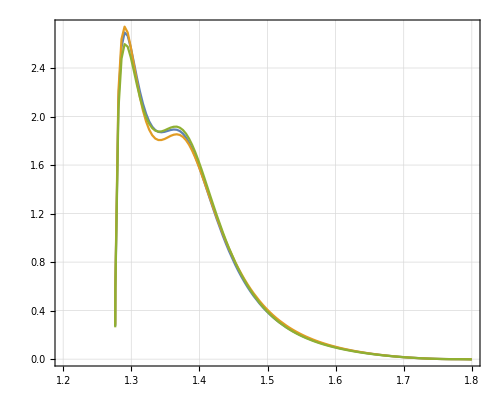

```mathematica
Plot[{NNT[x^2,0.0,0.0,FFωK,NVALUESωK],NNT[x^2,-0.01,0.0,FFωK,NVALUESωK],NNT[x^2,0.0,0.12,FFωK,NVALUESωK]},{x,1.2,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}\\frac{d\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\omega K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=0,\\hat{\\epsilon}_R=0.12"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.75,.85}],PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"dDR_OmegaK_NN.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/dDR_OmegaK_NN.pdf

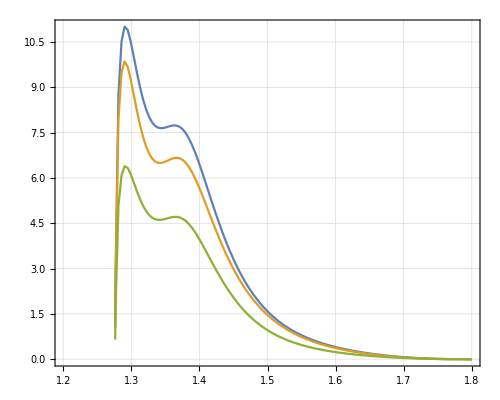

```mathematica
Plot[{10^4*ττ dΓsωK[x^2,0.0,0.0],10^4*ττ dΓsωK[x^2,-0.01,0.0],10^4*ττ dΓsωK[x^2,0.0,0.12]},{x,1.2,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d\\Gamma}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\omega K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\epsilon_T=\\epsilon_R=0","\\epsilon_T=-0.01,\\epsilon_R=0","\\epsilon_T=0,\\epsilon_R=0.12"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.75,.85}],PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"dDR_OmegaK.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/dDR_OmegaK.pdf

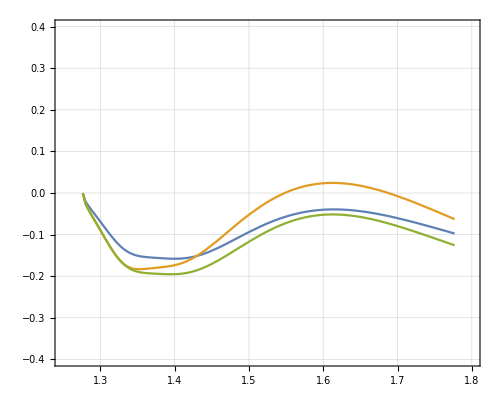

```mathematica
Plot[{AFBωKT[x^2,0,0],AFBωKT[x^2,-0.01,0],AFBωKT[x^2,0,0.12]},{x,mp+mV/.NVALUESωK,mτ/.NVALUESωK},FrameLabel->{{MaTeX["\\textrm{A}_{\\textrm{FB}}(s)",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\omega K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_R=0.12,\\hat{\\epsilon}_T=0"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.7,.8}],PlotRange->{{1.25,1.8},{-.4,.4}},PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"AFB_OmegaK.pdf"}],%]
```

/home/diego/AFB_OmegaK.pdf

```mathematica
min=0.0;
max=0.008;
ramp=ColorData["Rainbow"];
plotCF=ramp[Rescale[Last@{##},{min,max}]]&;
legendCF=ramp[Rescale[#,{min,max}]]&;
legend=Placed[BarLegend[{legendCF,{min,max}}],After];
```

```mathematica
Plt1=DensityPlot[Piecewise[{{ττ*d2ΓωK[saux,taux,0.0,0.0],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωK]}},Null],{saux,(mV+mp)^2/.NVALUESωK,mτ^2/.NVALUESωK},{taux,(mp)^2/.NVALUESωK,(mτ-mV)^2/.NVALUESωK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_OmegaK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_OmegaK_1.pdf

```mathematica
Plt2=DensityPlot[Piecewise[{{ττ*d2ΓωK[saux,taux,-0.01,0.0],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωK]}},Null],{saux,(mV+mp)^2/.NVALUESωK,mτ^2/.NVALUESωK},{taux,(mp)^2/.NVALUESωK,(mτ-mV)^2/.NVALUESωK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=-0.07,\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_OmegaK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_OmegaK_2.pdf

```mathematica
Plt3=DensityPlot[Piecewise[{{ττ*d2ΓωK[saux,taux,0.0,-0.12],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωK]}},Null],{saux,(mV+mp)^2/.NVALUESωK,mτ^2/.NVALUESωK},{taux,(mp)^2/.NVALUESωK,(mτ-mV)^2/.NVALUESωK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=0,\\epsilon_R=-0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_OmegaK_3.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_OmegaK_3.pdf

```mathematica
GraphicsRow[{Plt1,Plt2,Plt3},ImageSize->1790]
```

-Graphics-

```mathematica
Plt1=DensityPlot[10ττ d2ΓωKdCθ[saux,Cθ,0.0,0.0],{saux,(mV+mp)^2/.NVALUESωK,mτ^2/.NVALUESωK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["10\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_OmegaK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_OmegaK_1.pdf

```mathematica
Plt2=DensityPlot[10ττ d2ΓωKdCθ[saux,Cθ,-0.01,0.0],{saux,(mV+mp)^2/.NVALUESωK,mτ^2/.NVALUESωK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["10\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=-0.07,\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_OmegaK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_OmegaK_2.pdf

```mathematica
Plt3=DensityPlot[10ττ d2ΓωKdCθ[saux,Cθ,0.0,0.12],{saux,(mV+mp)^2/.NVALUESωK,mτ^2/.NVALUESωK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["10\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=0,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_OmegaK_3.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_OmegaK_3.pdf

```mathematica
GraphicsRow[{Plt1,Plt2,Plt3},ImageSize->1790]
```

-Graphics-

```mathematica
min=0.0;
max=0.63;
ramp=ColorData["Rainbow"];
plotCF=ramp[Rescale[Last@{##},{min,max}]]&;
legendCF=ramp[Rescale[#,{min,max}]]&;
legend=Placed[BarLegend[{legendCF,{min,max}}],After];
```

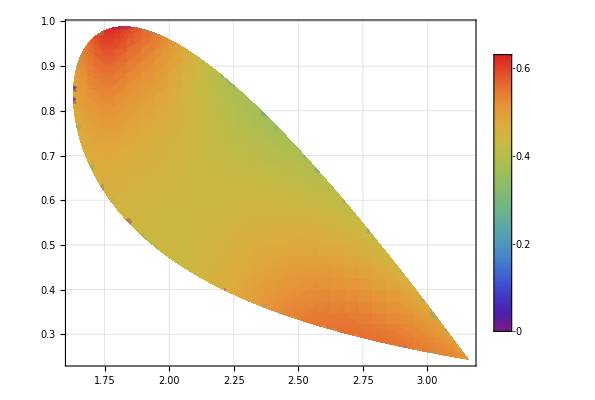

```mathematica
DensityPlot[Piecewise[{{ΔtT[saux,taux,-0.01,0.12,FFωK,NVALUESωK],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESωK]}},Null],{saux,(mV+mp)^2/.NVALUESωK,mτ^2/.NVALUESωK},{taux,(mp)^2/.NVALUESωK,(mτ-mV)^2/.NVALUESωK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\tilde{\\Delta}(\\epsilon_{T}=-0.01,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_Delta_OmegaK_1.pdf"}],%]
```

/home/diego/Dalitz_Delta_OmegaK_1.pdf

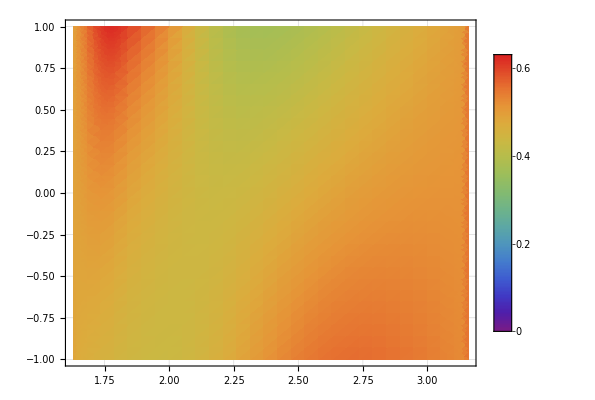

```mathematica
DensityPlot[ΔtθT[saux,xaux,-0.01,0.12,FFωK,NVALUESωK],{saux,(mV+mp)^2/.NVALUESωK,mτ^2/.NVALUESωK},{xaux,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\tilde{\\Delta}(\\epsilon_{T}=-0.01,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_Delta_OmegaK_2.pdf"}],%]
```

/home/diego/Dalitz_Delta_OmegaK_2.pdf

```mathematica
BRωKSim[ϵT_,ϵR_]:=FR1[[1]]+(1-ϵR)^2 FR1[[2]]+4 ϵT^2 FR1[[3]]-(1-ϵR)FR2[[1]]+2ϵT FR2[[2]]-(1-ϵR)2 ϵT FR2[[3]];
```

```mathematica
ΔωKSim[ϵT_,ϵR_]:=BRωKSim[ϵT,ϵR]/BRωKSim[0.0,0.0]-1.0;
```

```mathematica
ΔωKSim[0,0]
```

-1.11022×10^-16

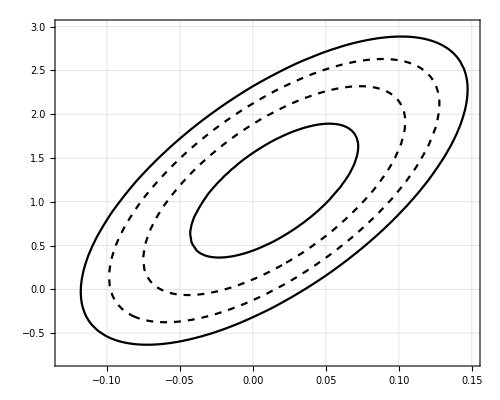

```mathematica
ContourPlot[{ΔωKSim[ϵT,ϵR]==(4.1+3 0.9)/4.0-1,ΔωKSim[ϵT,ϵR]==(4.1-3 0.9)/4.0-1,ΔωKSim[ϵT,ϵR]==(4.1+0.9)/4.0-1,ΔωKSim[ϵT,ϵR]==(4.1-0.9)/4.0-1},{ϵT,-.13,.15},{ϵR,-.8,3},GridLines->Automatic,FrameLabel->{{MaTeX["\\epsilon_R",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX["\\tau^-\\to\\omega K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},ContourStyle->{Black,Black,{Dashed,Black},{Dashed,Black}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ER_OmegaK.pdf"}],%]
```

/home/diego/ER_OmegaK.pdf

```mathematica
PltBr1=Plot[{ΔωKSim[0.0,ϵR],(4.1+3 0.9)/4-1.0,(4.1-3 0.9)/4.0-1,(4.1+0.9)/4.0-1,(4.1-0.9)/4.0-1.},{ϵR,-.35,2.5},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\Delta(\\tau^-\\to \\omega K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_R",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Delta_OmegaK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Delta_OmegaK_1.pdf

```mathematica
PltBr2=Plot[{ΔωKSim[ϵT,0.0],(4.1+3 0.9)/4.0-1,(4.1-3 0.9)/4.0-1,(4.1+0.9)/4.0-1,(4.1-0.9)/4.0-1},{ϵT,-.15,.05},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\Delta(\\tau^-\\to \\omega K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Delta_OmegaK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Delta_OmegaK_2.pdf

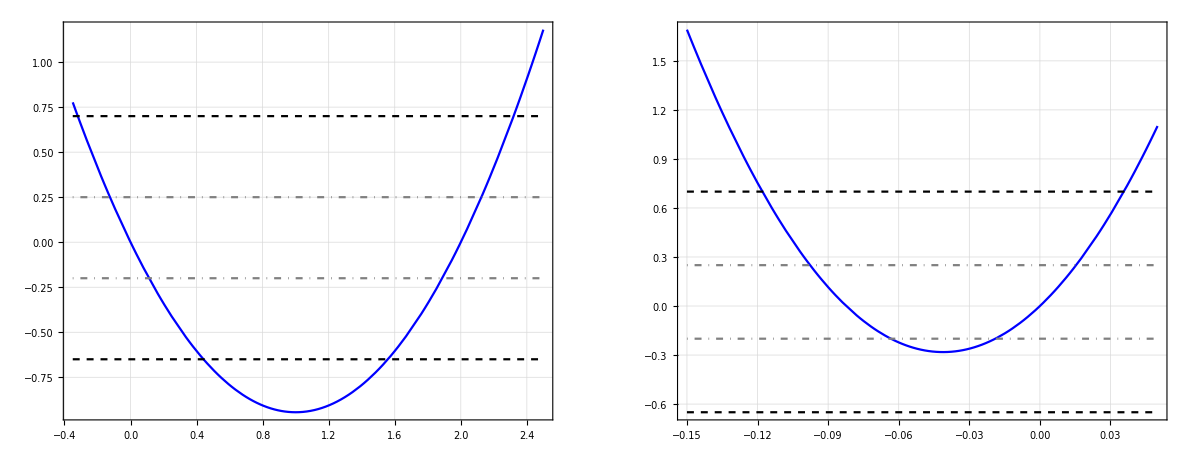

```mathematica
GraphicsRow[{PltBr1,PltBr2},ImageSize->1190]
```

### τ^-→ ρK^-(ν̄)_τ

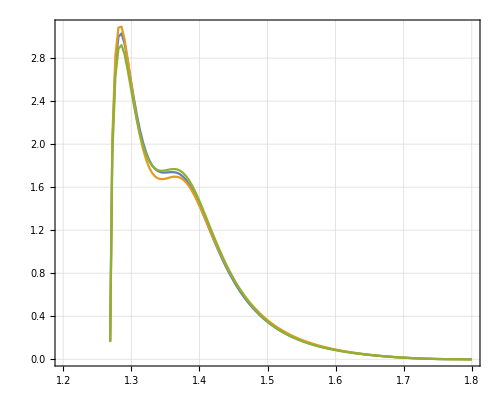

```mathematica
Plot[{NNT[x^2,0.0,0.0,FFρK,NVALUESρK],NNT[x^2,-0.01,0.0,FFρK,NVALUESρK],NNT[x^2,0.0,0.12,FFρK,NVALUESρK]},{x,1.2,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}\\frac{d\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\rho K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=0,\\hat{\\epsilon}_R=0.12"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.75,.85}],PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"dDR_RhoK_NN.pdf"}],%];
```

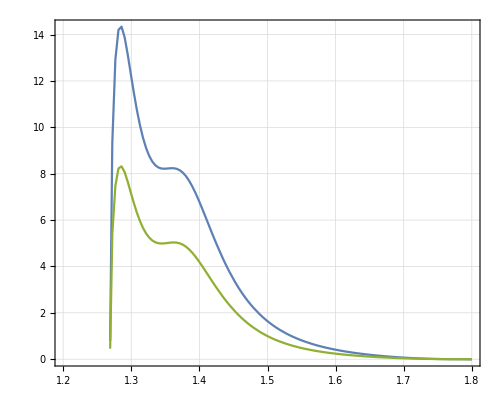

```mathematica
Plot[{10^4*ττ dΓT[x^2,0.0,0.0,FFρK,NVALUESρK],10^4*ττ dΓT[x^2,-0.01,0.0FFρK,NVALUESρK],10^4*ττ dΓT[x^2,0.0,0.12,FFρK,NVALUESρK]},{x,1.2,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d\\Gamma}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\rho K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\epsilon_T=\\epsilon_R=0","\\epsilon_T=-0.01,\\epsilon_R=0","\\epsilon_T=0,\\epsilon_R=0.12"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.75,.85}],PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"dDR_RhoK.pdf"}],%]
```

/home/diego/dDR_RhoK.pdf

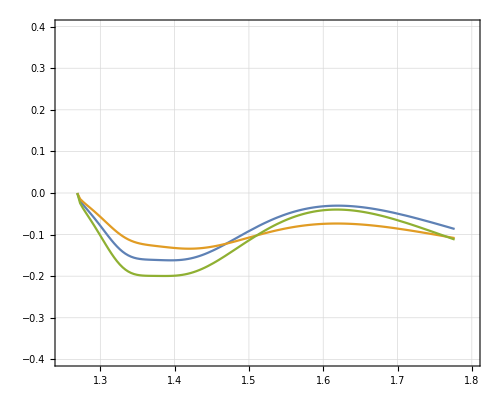

```mathematica
Plot[{AFBT[x^2,0,0,FFρK,NVALUESρK],AFBT[x^2,0.01,0,FFρK,NVALUESρK],AFBT[x^2,0,0.12,FFρK,NVALUESρK]},{x,mp+mV/.NVALUESρK,mτ/.NVALUESρK},FrameLabel->{{MaTeX["\\textrm{A}_{\\textrm{FB}}(s)",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\rho K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_R=0.12,\\hat{\\epsilon}_T=0"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.7,.8}],PlotRange->{{1.25,1.8},{-.4,.4}},PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"AFB_RhoK.pdf"}],%]
```

/home/diego/AFB_RhoK.pdf

```mathematica
PltBr1=Plot[{BRT[0.0,ϵR,FFρK,NVALUESρK],(1.6+3 0.6)10^-3,(1.6-3 0.6)10^-3,(1.6+0.6)10^-3,(1.6-0.6)10^-3},{ϵR,-1,2},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\textrm{BR}(\\tau^-\\to \\rho K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_R",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"BR_RhoK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/BR_RhoK_1.pdf

```mathematica
PltBr2=Plot[{BRT[ϵT,0.0,FFρK,NVALUESρK],(1.6+3 0.6)10^-3,(1.6-3 0.6)10^-3,(1.6+0.6)10^-3,(1.6-0.6)10^-3},{ϵT,-.3,.2},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\textrm{BR}(\\tau^-\\to \\rho K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"BR_RhoK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/BR_RhoK_2.pdf

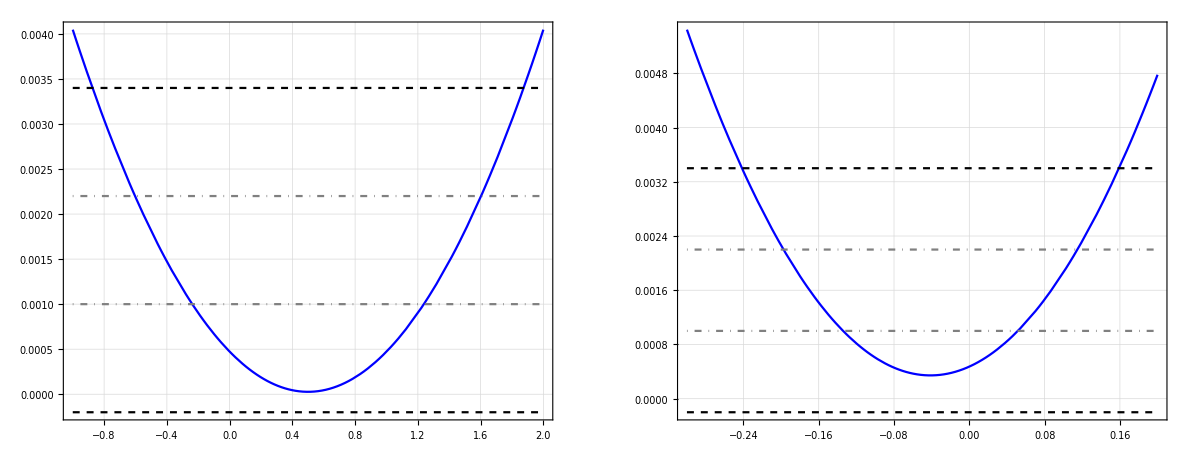

```mathematica
GraphicsRow[{PltBr1,PltBr2},ImageSize->1190]
```

```mathematica
min=0.0;
max=0.0087;
ramp=ColorData["Rainbow"];
plotCF=ramp[Rescale[Last@{##},{min,max}]]&;
legendCF=ramp[Rescale[#,{min,max}]]&;
legend=Placed[BarLegend[{legendCF,{min,max}}],After];
```

```mathematica
Plt1=DensityPlot[Piecewise[{{ττ*d2ΓT[saux,taux,0.0,0.0,FFρK,NVALUESρK],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESρK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESρK]}},Null],{saux,(mV+mp)^2/.NVALUESρK,mτ^2/.NVALUESρK},{taux,(mp)^2/.NVALUESρK,(mτ-mV)^2/.NVALUESρK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_RhoK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_RhoK_1.pdf

```mathematica
Plt2=DensityPlot[Piecewise[{{ττ*d2ΓT[saux,taux,-0.07,0.0,FFρK,NVALUESρK],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESρK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESρK]}},Null],{saux,(mV+mp)^2/.NVALUESρK,mτ^2/.NVALUESρK},{taux,(mp)^2/.NVALUESρK,(mτ-mV)^2/.NVALUESρK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=-0.07,\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_RhoK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_RhoK_2.pdf

```mathematica
Plt3=DensityPlot[Piecewise[{{ττ*d2ΓT[saux,taux,0.0,0.12,FFρK,NVALUESρK],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESρK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESρK]}},Null],{saux,(mV+mp)^2/.NVALUESρK,mτ^2/.NVALUESρK},{taux,(mp)^2/.NVALUESρK,(mτ-mV)^2/.NVALUESρK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=0,\\epsilon_R=-0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_RhoK_3.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_RhoK_3.pdf

```mathematica
GraphicsRow[{Plt1,Plt2,Plt3},ImageSize->1790]
```

-Graphics-

```mathematica
Plt1=DensityPlot[10ττ d2ΓCθT[saux,Cθ,0.0,0.0,FFρK,NVALUESρK],{saux,(mV+mp)^2/.NVALUESρK,mτ^2/.NVALUESρK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["10\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_RhoK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_RhoK_1.pdf

```mathematica
Plt2=DensityPlot[10ττ d2ΓCθT[saux,Cθ,-0.01,0.0,FFρK,NVALUESρK],{saux,(mV+mp)^2/.NVALUESρK,mτ^2/.NVALUESρK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["10\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=-0.07,\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_RhoK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_RhoK_2.pdf

```mathematica
Plt3=DensityPlot[10ττ d2ΓCθT[saux,Cθ,0.0,0.12,FFρK,NVALUESρK],{saux,(mV+mp)^2/.NVALUESρK,mτ^2/.NVALUESρK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["10\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=0,\\epsilon_R=0.012)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_RhoK_3.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_RhoK_3.pdf

```mathematica
GraphicsRow[{Plt1,Plt2,Plt3},ImageSize->1790]
```

-Graphics-

```mathematica
min=0.0;
max=0.63;
ramp=ColorData["Rainbow"];
plotCF=ramp[Rescale[Last@{##},{min,max}]]&;
legendCF=ramp[Rescale[#,{min,max}]]&;
legend=Placed[BarLegend[{legendCF,{min,max}}],After];
```

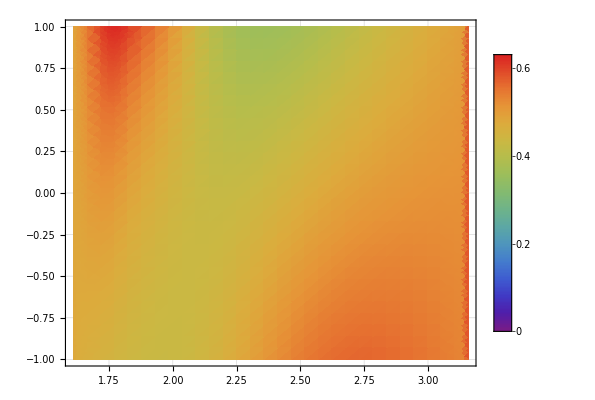

```mathematica
DensityPlot[ΔtθT[saux,Cθ,-0.01,0.12,FFρK,NVALUESρK],{saux,(mV+mp)^2/.NVALUESρK,mτ^2/.NVALUESρK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\tilde{\\Delta}(\\epsilon_{T}=-0.01\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_Delta_RhoK_1.pdf"}],%]
```

/home/diego/Dalitz_Delta_RhoK_1.pdf

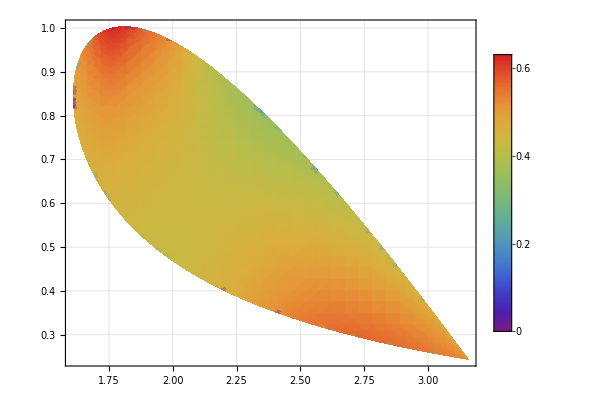

```mathematica
DensityPlot[Piecewise[{{ΔtT[saux,taux,-0.01,0.12,FFρK,NVALUESρK],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESρK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESρK]}},Null],{saux,(mV+mp)^2/.NVALUESρK,mτ^2/.NVALUESρK},{taux,mp^2/.NVALUESρK,(mτ-mV)^2/.NVALUESρK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\tilde{\\Delta}(\\epsilon_{T}=-0.01,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_Delta_RhoK_2.pdf"}],%]
```

/home/diego/Dalitz_Delta_RhoK_2.pdf

```mathematica
α=FFR[FFρK,NVALUESρK];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 51 recursive bisections in saux near {saux} = {1.}. NIntegrate obtained 0 and 0 for the integral and error estimates.

```mathematica
BRρKSim[ϵT_,ϵR_]:=α[[1]]+(1-ϵR)^2 α[[2]]+4 ϵT^2 α[[3]]-(1-ϵR)α[[4]]+2ϵT α[[5]]-(1-ϵR)2 ϵT α[[6]];
```

```mathematica
ΔρKSim[ϵT_,ϵR_]:=BRρKSim[ϵT,ϵR]/BRρKSim[0.0,0.0]-1.0;
```

```mathematica
ΔρKSim[0,0]
```

0.

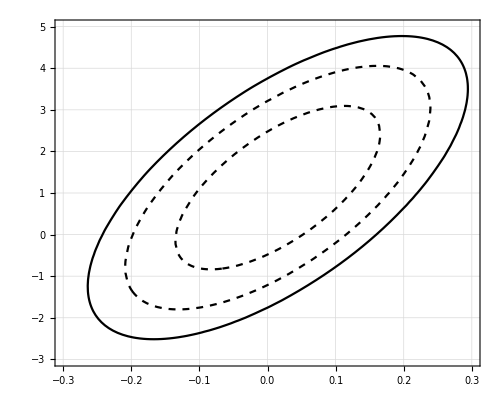

```mathematica
ContourPlot[{ΔρKSim[ϵT,ϵR]==(1.6+3 0.6)/(.47)-1,ΔρKSim[ϵT,ϵR]==(1.6-3 0.6)/(.47)-1,ΔρKSim[ϵT,ϵR]==(1.6+0.6)/(.47)-1,ΔρKSim[ϵT,ϵR]==(1.6-0.6)/(.47)-1},{ϵT,-.3,.3},{ϵR,-3,5},GridLines->Automatic,FrameLabel->{{MaTeX["\\epsilon_R",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX["\\tau^-\\to\\rho K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},ContourStyle->{Black,Black,{Dashed,Black},{Dashed,Black}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ER_RhoK.pdf"}],%]
```

/home/diego/ER_RhoK.pdf

```mathematica
PltBr1=Plot[{ΔρKSim[0.0,ϵR],(1.6+3 0.6)/(.47)-1,(1.6-3 0.6)/(.47)-1,(1.6+0.6)/(.47)-1,(1.6-0.6)/(.47)-1},{ϵR,-2,4.2},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\Delta(\\tau^-\\to \\rho K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_R",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Delta_RhoK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Delta_RhoK_1.pdf

```mathematica
PltBr2=Plot[{ΔρKSim[ϵT,0.0],(1.6+3 0.6)/(.47)-1,(1.6-3 0.6)/(.47)-1,(1.6+0.6)/(.47)-1,(1.6-0.6)/(.47)-1},{ϵT,-.3,.2},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\Delta(\\tau^-\\to \\rho K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Delta_RhoK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Delta_RhoK_2.pdf

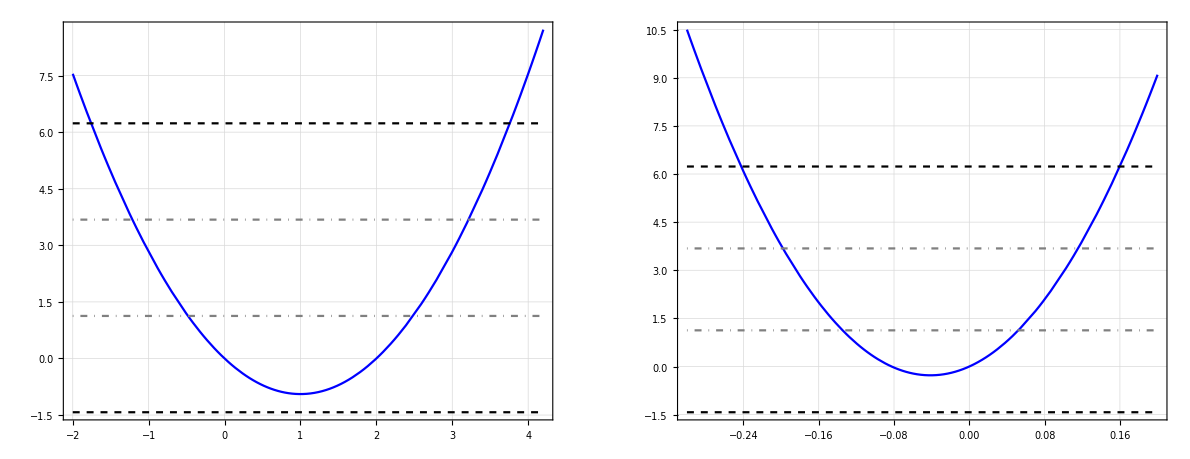

```mathematica
GraphicsRow[{PltBr1,PltBr2},ImageSize->1190]
```

### τ^-→(K̄)^*π^-(ν̄)_τ

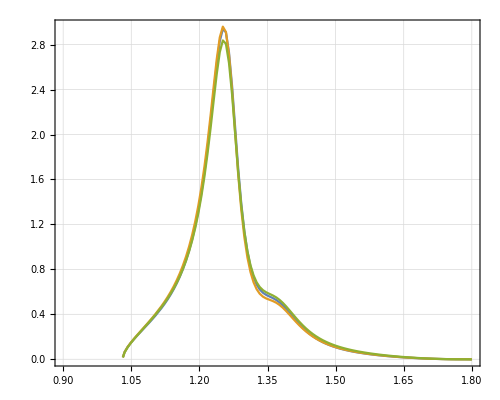

```mathematica
Plot[{NNT[x^2,0.0,0.0,FFKsπ,NVALUESKsπ],NNT[x^2,-0.01,0.0,FFKsπ,NVALUESKsπ],NNT[x^2,0.0,0.12,FFKsπ,NVALUESKsπ]},{x,.9,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}\\frac{d\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\overline{K}^* \\pi^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=0,\\hat{\\epsilon}_R=0.12"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.75,.85}],PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"dDR_KsPi_NN.pdf"}],%];
```

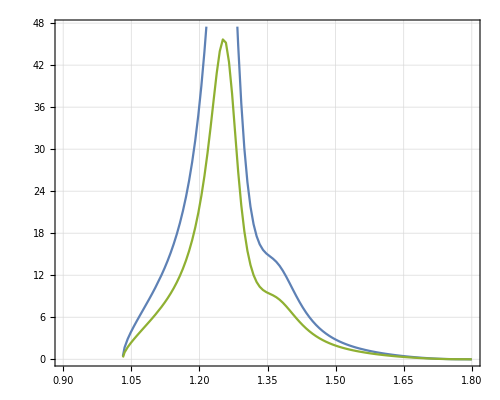

```mathematica
Plot[{10^4*ττ dΓT[x^2,0.0,0.0,FFKsπ,NVALUESKsπ],10^4*ττ dΓT[x^2,-0.01,0.0FFKsπ,NVALUESKsπ],10^4*ττ dΓT[x^2,0.0,0.12,FFKsπ,NVALUESKsπ]},{x,.9,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d\\Gamma}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\overline{K}^* \\pi^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\epsilon_T=0,\\epsilon_R=0.12"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.75,.85}],PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"dDR_KsPi.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/dDR_KsPi.pdf

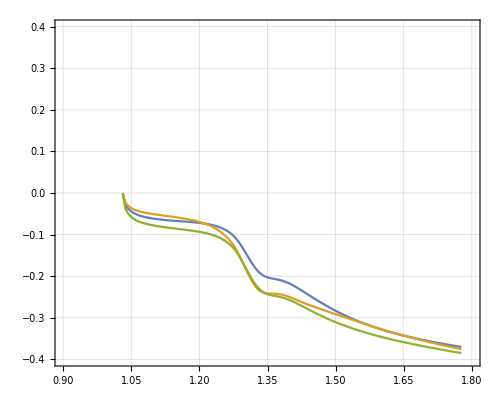

```mathematica
Plot[{AFBT[x^2,0,0,FFKsπ,NVALUESKsπ],AFBT[x^2,-0.01,0,FFKsπ,NVALUESKsπ],AFBT[x^2,0,0.12,FFKsπ,NVALUESKsπ]},{x,mp+mV/.NVALUESKsπ,mτ/.NVALUESKsπ},FrameLabel->{{MaTeX["\\textrm{A}_{\\textrm{FB}}(s)",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\overline{K}^* \\pi^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_R=0.12,\\hat{\\epsilon}_T=0"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.75,.85}],PlotRange->{{.9,1.8},{-.4,.4}},PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"AFB_KsPi.pdf"}],%]
```

/home/diego/AFB_KsPi.pdf

```mathematica
PltBr1=Plot[{BRT[0.0,ϵR,FFKsπ,NVALUESKsπ],(2.2+3 0.5)10^-3,(2.2-3 0.5)10^-3,(2.2+0.5)10^-3,(2.2-0.5)10^-3},{ϵR,-1.2,1.2},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\textrm{BR}(\\tau^-\\to \\overline{K}^* \\pi^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_R",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"BR_KsPi_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/BR_KsPi_1.pdf

```mathematica
PltBr2=Plot[{BRT[ϵT,0.0,FFKsπ,NVALUESKsπ],(2.2+3 0.5)10^-3,(2.2-3 0.5)10^-3,(2.2+0.5)10^-3,(2.2-0.5)10^-3},{ϵT,-.15,.15},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\textrm{BR}(\\tau^-\\to \\overline{K}^* \\pi^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"BR_KsPi_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/BR_KsPi_2.pdf

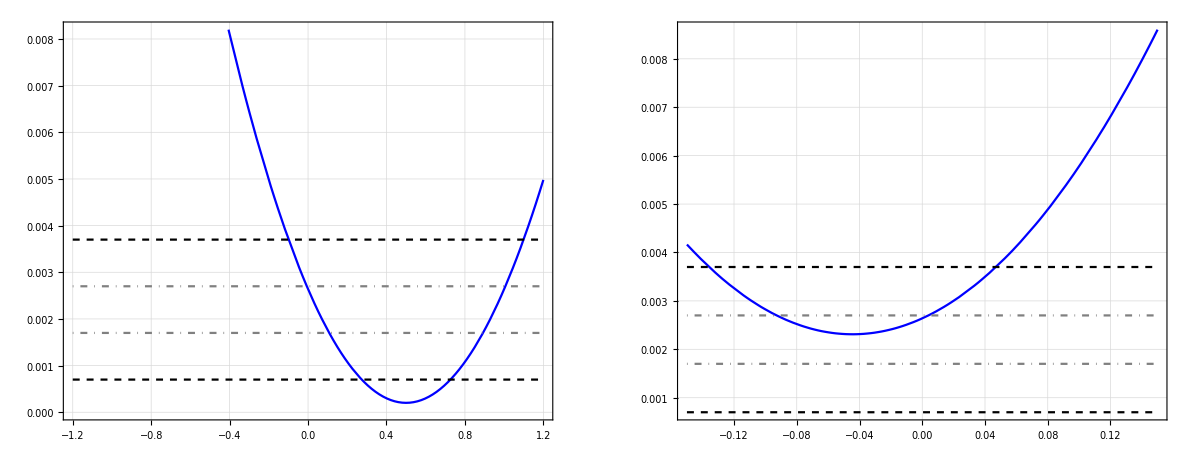

```mathematica
GraphicsRow[{PltBr1,PltBr2},ImageSize->1190]
```

```mathematica
min=0.0;
max=0.013;
ramp=ColorData["Rainbow"];
plotCF=ramp[Rescale[Last@{##},{min,max}]]&;
legendCF=ramp[Rescale[#,{min,max}]]&;
legend=Placed[BarLegend[{legendCF,{min,max}}],After];
```

```mathematica
Plt1=DensityPlot[Piecewise[{{ττ*d2ΓT[saux,taux,0.0,0.0,FFKsπ,NVALUESKsπ],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsπ]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsπ]}},Null],{saux,(mV+mp)^2/.NVALUESKsπ,mτ^2/.NVALUESKsπ},{taux,(mp)^2/.NVALUESKsπ,(mτ-mV)^2/.NVALUESKsπ},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["t[\\textrm{GeV}]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_KsPi_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_KsPi_1.pdf

```mathematica
Plt2=DensityPlot[Piecewise[{{ττ*d2ΓT[saux,taux,-0.01,0.0,FFKsπ,NVALUESKsπ],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsπ]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsπ]}},Null],{saux,(mV+mp)^2/.NVALUESKsπ,mτ^2/.NVALUESKsπ},{taux,(mp)^2/.NVALUESKsπ,(mτ-mV)^2/.NVALUESKsπ},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["t[\\textrm{GeV}]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=-0.7,\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_KsPi_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_KsPi_2.pdf

```mathematica
Plt3=DensityPlot[Piecewise[{{ττ*d2ΓT[saux,taux,0.0,0.12,FFKsπ,NVALUESKsπ],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsπ]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsπ]}},Null],{saux,(mV+mp)^2/.NVALUESKsπ,mτ^2/.NVALUESKsπ},{taux,(mp)^2/.NVALUESKsπ,(mτ-mV)^2/.NVALUESKsπ},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["t[\\textrm{GeV}]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=0,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_KsPi_3.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_KsPi_3.pdf

```mathematica
GraphicsRow[{Plt1,Plt2,Plt3},ImageSize->1790]
```

-Graphics-

```mathematica
Plt1=DensityPlot[5ττ d2ΓCθT[saux,Cθ,0.0,0.0,FFKsπ,NVALUESKsπ],{saux,(mV+mp)^2/.NVALUESKsπ,mτ^2/.NVALUESKsπ},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["5\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_KsPi_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_KsPi_1.pdf

```mathematica
Plt2=DensityPlot[5ττ d2ΓCθT[saux,Cθ,-0.01,0.0,FFKsπ,NVALUESKsπ],{saux,(mV+mp)^2/.NVALUESKsπ,mτ^2/.NVALUESKsπ},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["5\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=-0.01,\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_KsPi_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_KsPi_2.pdf

```mathematica
Plt3=DensityPlot[5ττ d2ΓCθT[saux,Cθ,0.0,0.12,FFKsπ,NVALUESKsπ],{saux,(mV+mp)^2/.NVALUESKsπ,mτ^2/.NVALUESKsπ},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}]",Magnification->1.5],MaTeX["5\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=0,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_KsPi_3.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_KsPi_3.pdf

```mathematica
GraphicsRow[{Plt1,Plt2,Plt3},ImageSize->1790]
```

-Graphics-

```mathematica
min=0.0;
max=0.65;
ramp=ColorData["Rainbow"];
plotCF=ramp[Rescale[Last@{##},{min,max}]]&;
legendCF=ramp[Rescale[#,{min,max}]]&;
legend=Placed[BarLegend[{legendCF,{min,max}}],After];
```

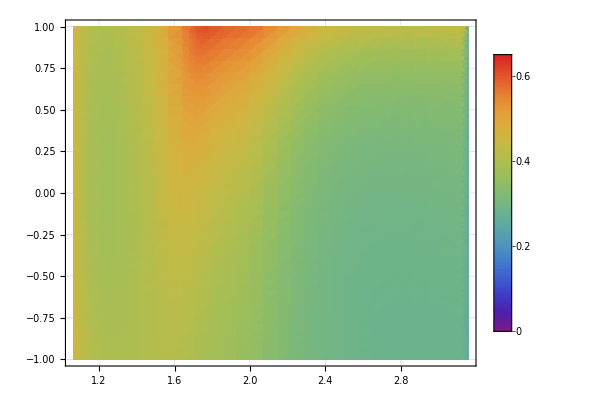

```mathematica
DensityPlot[ΔtθT[saux,Cθ,-0.01,0.12,FFKsπ,NVALUESKsπ],{saux,(mV+mp)^2/.NVALUESKsπ,mτ^2/.NVALUESKsπ},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\tilde{\\Delta}(\\epsilon_{T}=-0.01,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_Delta_KsPi_1.pdf"}],%]
```

/home/diego/Dalitz_Delta_KsPi_1.pdf

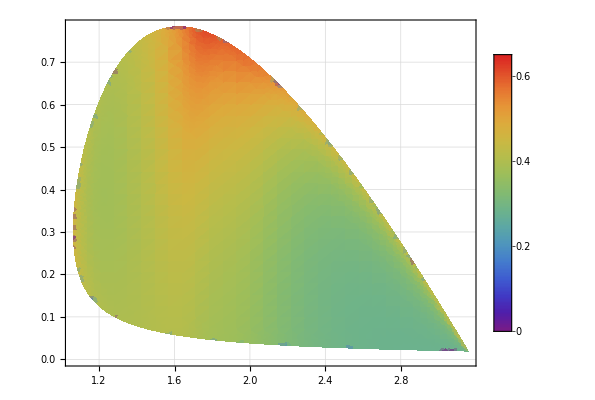

```mathematica
DensityPlot[Piecewise[{{ΔtT[saux,taux,-0.01,0.12,FFKsπ,NVALUESKsπ],N[tmin[mτ,0,mp,mV]/.{λ->λp}/.{s->saux}/.NVALUESKsπ]<taux<N[tmax[mτ,0,mp,mV]/.{λ->λp}/.{s->saux}/.NVALUESKsπ]}},Null],{saux,(mV+mp)^2/.NVALUESKsπ,mτ^2/.NVALUESKsπ},{taux,mp^2/.NVALUESKsπ,(mτ-mV)^2/.NVALUESKsπ},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->30,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\tilde{\\Delta}(\\epsilon_{T}=-0.01,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_Delta_KsPi_2.pdf"}],%]
```

/home/diego/Dalitz_Delta_KsPi_2.pdf

```mathematica
α=FFR[FFKsπ,NVALUESKsπ];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 51 recursive bisections in saux near {saux} = {1.}. NIntegrate obtained 0 and 0 for the integral and error estimates.

```mathematica
BRKsπSim[ϵT_,ϵR_]:=α[[1]]+(1-ϵR)^2 α[[2]]+4 ϵT^2 α[[3]]-(1-ϵR)α[[4]]+2ϵT α[[5]]-(1-ϵR)2 ϵT α[[6]];
```

```mathematica
ΔKsπSim[ϵT_,ϵR_]:=BRKsπSim[ϵT,ϵR]/BRKsπSim[0.0,0.0]-1.0;
```

```mathematica
ΔKsπSim[0,0]
```

-1.11022×10^-16

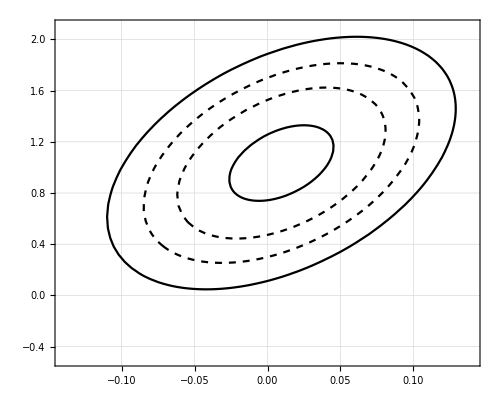

```mathematica
ContourPlot[{ΔKsπSim[ϵT,ϵR]==(2.6+3 0.5)/5.1-1,ΔKsπSim[ϵT,ϵR]==(2.2-3 0.5)/5.1-1,ΔKsπSim[ϵT,ϵR]==(2.2+0.5)/5.1-1,ΔKsπSim[ϵT,ϵR]==(2.2-0.5)/5.1-1},{ϵT,-.14,.14},{ϵR,-0.5,2.1},GridLines->Automatic,FrameLabel->{{MaTeX["\\epsilon_R",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX["\\tau^-\\to\\overline{K}^* \\pi^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},ContourStyle->{Black,Black,{Dashed,Black},{Dashed,Black}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ER_KsPi.pdf"}],%]
```

/home/diego/ER_KsPi.pdf

```mathematica
PltBr1=Plot[{ΔKsπSim[0.0,ϵR],(2.2+3 0.5)/5.1-1,(2.2-3 0.5)/5.1-1,(2.2+0.5)/5.1-1,(2.2-0.5)/5.1-1},{ϵR,-.15,2},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\Delta(\\tau^-\\to \\overline{K}^* \\pi^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_R",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Delta_KsPi_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Delta_KsPi_1.pdf

```mathematica
PltBr2=Plot[{ΔKsπSim[ϵT,0.0],(2.2+3 0.5)/5.1-1,(2.2-3 0.5)/5.1-1,(2.2+0.5)/5.1-1,(2.2-0.5)/5.1-1},{ϵT,-.15,.15},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\Delta(\\tau^-\\to \\overline{K}^* \\pi^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Delta_KsPi_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Delta_KsPi_2.pdf

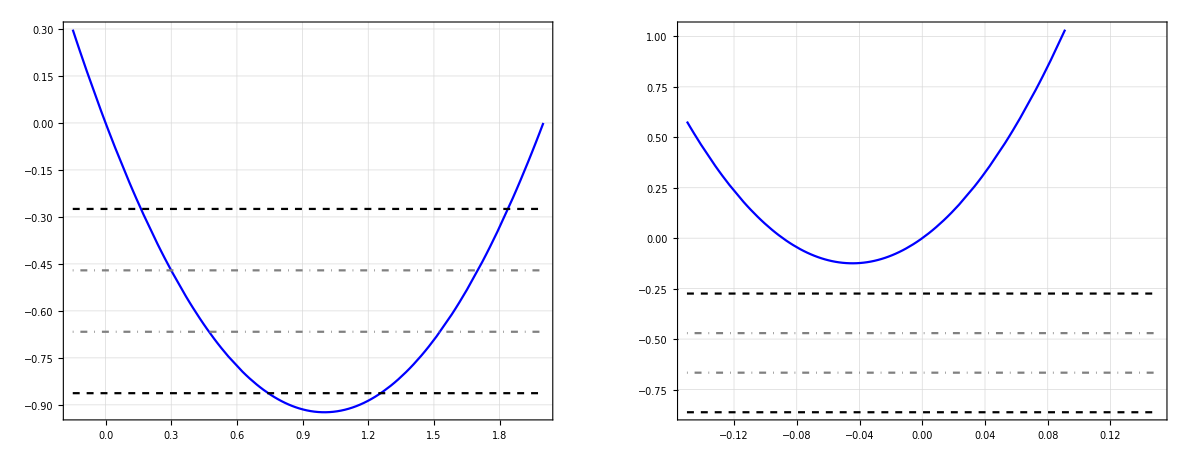

```mathematica
GraphicsRow[{PltBr1,PltBr2},ImageSize->1190]
```

### τ^-→(K̄)^*K^-(ν̄)_τ

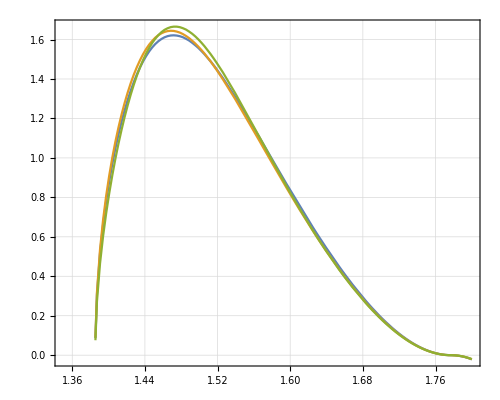

```mathematica
Plot[{NNT[x^2,0.0,0.0,FFKsK,NVALUESKsK],NNT[x^2,-0.01,0.0,FFKsK,NVALUESKsK],NNT[x^2,0.0,0.12,FFKsK,NVALUESKsK]},{x,1.35,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}\\frac{d\\Gamma(\\hat{\\epsilon}_R,\\hat{\\epsilon}_T)}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\overline{K}^* K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=0,\\hat{\\epsilon}_R=0.12"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.75,.85}],PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"dDR_KsK_NN.pdf"}],%];
```

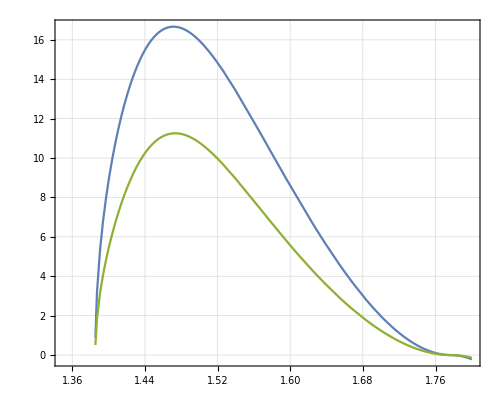

```mathematica
Plot[{10^4*ττ dΓT[x^2,0.0,0.0,FFKsK,NVALUESKsK],10^4*ττ dΓT[x^2,-0.01,0.0FFKsK,NVALUESKsK],10^4*ττ dΓT[x^2,0.0,0.12,FFKsK,NVALUESKsK]},{x,1.35,1.8},FrameLabel->{{MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d\\Gamma}{ds}",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\overline{K}^* K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=0,\\hat{\\epsilon}_R=0.12"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.75,.85}],PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"dDR_KsK.pdf"}],%]
```

/home/diego/dDR_KsK.pdf

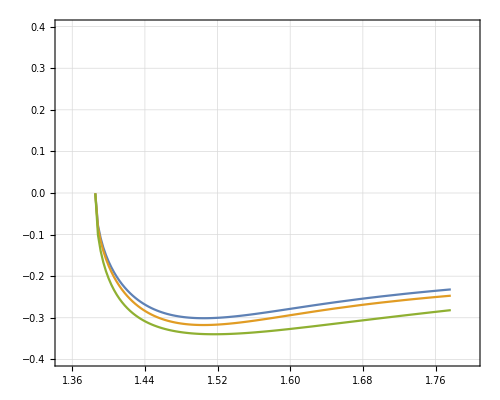

```mathematica
Plot[{AFBT[x^2,0,0,FFKsK,NVALUESKsK],AFBT[x^2,-0.01,0,FFKsK,NVALUESKsK],AFBT[x^2,0,0.12,FFKsK,NVALUESKsK]},{x,mp+mV/.NVALUESKsK,mτ/.NVALUESKsK},FrameLabel->{{MaTeX["\\textrm{A}_{\\textrm{FB}}(s)",Magnification->1.5]," "},{MaTeX["\\sqrt{s} \\,[\\textrm{GeV}]",Magnification->1.5],MaTeX["\\tau^-\\to\\overline{K}^* K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},GridLines->Automatic,PlotLegends->Placed[LineLegend[MaTeX[{"\\hat{\\epsilon}_T=\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_T=-0.01,\\hat{\\epsilon}_R=0","\\hat{\\epsilon}_R=0.12,\\hat{\\epsilon}_T=0"},Magnification->1.5],LegendMargins->0,LegendLabel->MaTeX[" "],LabelStyle->3],{.7,.85}],PlotRange->{{1.35,1.8},{-.4,.4}},PlotPoints->3]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"AFB_KsK.pdf"}],%]
```

/home/diego/AFB_KsK.pdf

```mathematica
PltBr1=Plot[{BRT[0.0,ϵR,FFKsK,NVALUESKsK],(2.1+3 0.4)10^-3,(2.1-3 0.4)10^-3,(2.1+0.4)10^-3,(2.1-0.4)10^-3},{ϵR,-.5,1.5},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\textrm{BR}(\\tau^-\\to \\overline{K}^* K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_R",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"BR_KsK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/BR_KsK_1.pdf

```mathematica
PltBr2=Plot[{BRT[ϵT,0.0,FFKsK,NVALUESKsK],(2.1+3 0.4)10^-3,(2.1-3 0.4)10^-3,(2.1+0.4)10^-3,(2.1-0.4)10^-3},{ϵT,-.3,.2},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\textrm{BR}(\\tau^-\\to \\overline{K}^* K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"BR_KsK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/BR_KsK_2.pdf

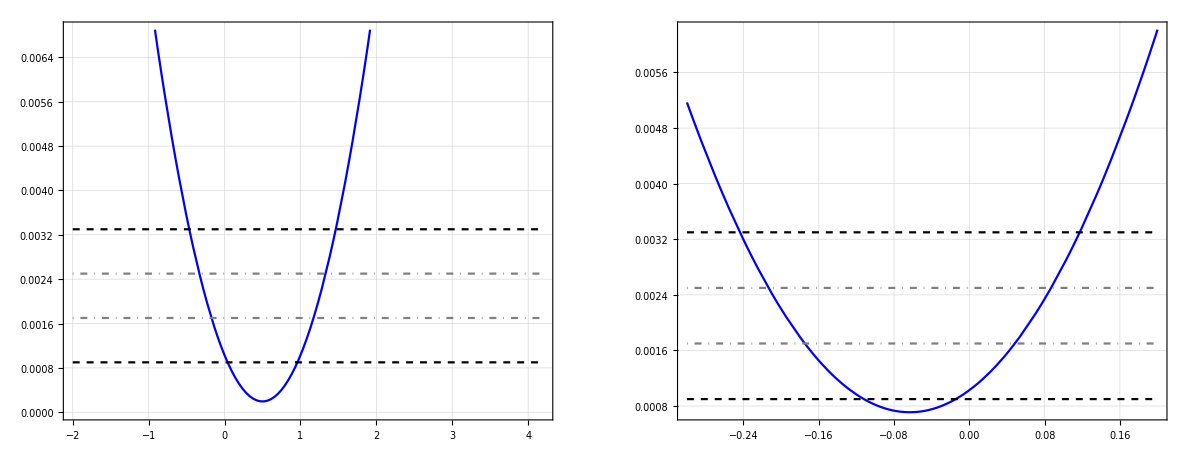

```mathematica
GraphicsRow[{PltBr1,PltBr2},ImageSize->1190]
```

```mathematica
min=0.0;
max=0.009;
ramp=ColorData["Rainbow"];
plotCF=ramp[Rescale[Last@{##},{min,max}]]&;
legendCF=ramp[Rescale[#,{min,max}]]&;
legend=Placed[BarLegend[{legendCF,{min,max}}],After];
```

```mathematica
Plt1=DensityPlot[Piecewise[{{ττ*Abs[d2ΓT[saux,taux,0.0,0.0,FFKsK,NVALUESKsK]],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsK]}},Null],{saux,(mV+mp)^2/.NVALUESKsK,mτ^2/.NVALUESKsK},{taux,(mp)^2/.NVALUESKsK,(mτ-mV)^2/.NVALUESKsK},PlotPoints->20,PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_KsK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_KsK_1.pdf

```mathematica
Plt2=DensityPlot[Piecewise[{{ττ*Abs[d2ΓT[saux,taux,-0.01,0.0,FFKsK,NVALUESKsK]],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsK]}},Null],{saux,(mV+mp)^2/.NVALUESKsK,mτ^2/.NVALUESKsK},{taux,(mp)^2/.NVALUESKsK,(mτ-mV)^2/.NVALUESKsK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=-0.01,\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_KsK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_KsK_2.pdf

```mathematica
Plt3=DensityPlot[Piecewise[{{ττ*Abs[d2ΓT[saux,taux,0.0,0.12,FFKsK,NVALUESKsK]],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsK]≤ taux≤N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsK]}},Null],{saux,(mV+mp)^2/.NVALUESKsK,mτ^2/.NVALUESKsK},{taux,(mp)^2/.NVALUESKsK,(mτ-mV)^2/.NVALUESKsK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsdt}(\\epsilon_{T}=0,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_KsK_3.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Dalitz_KsK_3.pdf

```mathematica
GraphicsRow[{Plt1,Plt2,Plt3},ImageSize->1790]
```

-Graphics-

```mathematica
Plt1=DensityPlot[5ττ d2ΓCθT[saux,Cθ,0.0,0.0,FFKsK,NVALUESKsK],{saux,(mV+mp)^2/.NVALUESKsK,mτ^2/.NVALUESKsK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["5\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_KsK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_KsK_1.pdf

```mathematica
Plt2=DensityPlot[5ττ d2ΓCθT[saux,Cθ,-0.01,0.0,FFKsK,NVALUESKsK],{saux,(mV+mp)^2/.NVALUESKsK,mτ^2/.NVALUESKsK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["5\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=-0.01,\\epsilon_R=0)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_KsK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_KsK_2.pdf

```mathematica
Plt3=DensityPlot[5ττ d2ΓCθT[saux,Cθ,0.0,0.12,FFKsK,NVALUESKsK],{saux,(mV+mp)^2/.NVALUESKsK,mτ^2/.NVALUESKsK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["5\\cdot\\frac{1}{\\Gamma_{\\tau}}\\frac{d^2\\Gamma}{dsd\\cos\\theta}(\\epsilon_{T}=0,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DalitzTheta_KsK_3.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/DalitzTheta_KsK_3.pdf

```mathematica
GraphicsRow[{Plt1,Plt2,Plt3},ImageSize->1790]
```

-Graphics-

```mathematica
min=0.0;
max=0.63;
ramp=ColorData["Rainbow"];
plotCF=ramp[Rescale[Last@{##},{min,max}]]&;
legendCF=ramp[Rescale[#,{min,max}]]&;
legend=Placed[BarLegend[{legendCF,{min,max}}],After];
```

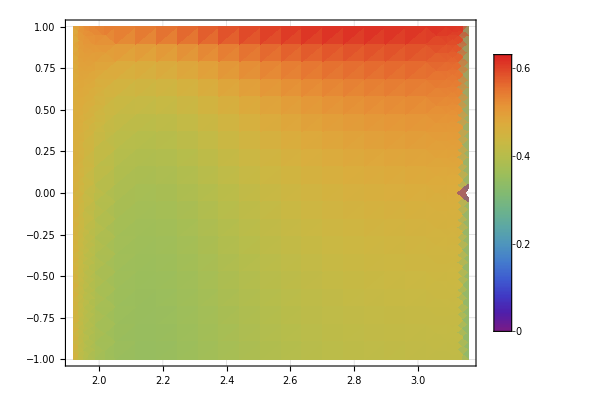

```mathematica
DensityPlot[ΔtθT[saux,Cθ,-0.01,0.12,FFKsK,NVALUESKsK],{saux,(mV+mp)^2/.NVALUESKsK,mτ^2/.NVALUESKsK},{Cθ,-1,1},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["\\cos\\theta",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\tilde{\\Delta}(\\epsilon_{T}=0,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_Delta_KsK_1.pdf"}],%]
```

/home/diego/Dalitz_Delta_KsK_1.pdf

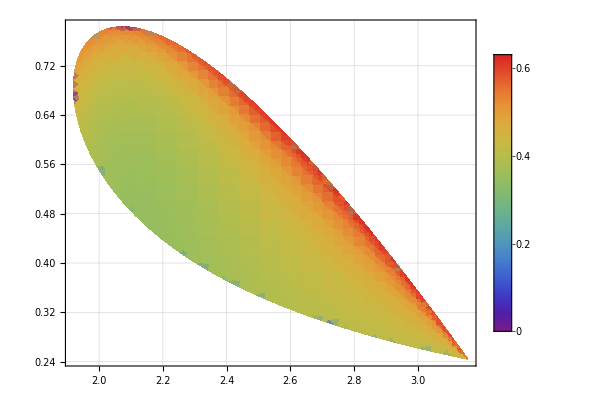

```mathematica
DensityPlot[Piecewise[{{ΔtT[saux,taux,-0.01,0.12,FFKsK,NVALUESKsK],N[tmin[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsK]<taux<N[tmax[mτ,0,mp,mV]/.λ->λp/.{s->saux}/.NVALUESKsK]}},Null],{saux,(mV+mp)^2/.NVALUESKsK,mτ^2/.NVALUESKsK},{taux,mp^2/.NVALUESKsK,(mτ-mV)^2/.NVALUESKsK},PlotRange->{min,max},ColorFunction->plotCF,ColorFunctionScaling->False,PlotPoints->20,FrameLabel->{{MaTeX["t[\\textrm{GeV}^2]",Magnification->1.5]," "},{MaTeX["s[\\textrm{GeV}^2]",Magnification->1.5],MaTeX["\\tilde{\\Delta}(\\epsilon_{T}=0,\\epsilon_R=0.12)",Magnification->1.5]}},GridLines->Automatic,PlotLegends->legend]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Dalitz_Delta_KsK_2.pdf"}],%]
```

/home/diego/Dalitz_Delta_KsK_2.pdf

```mathematica
α=FFR[FFKsK,NVALUESKsK];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 51 recursive bisections in saux near {saux} = {1.}. NIntegrate obtained 0 and 0 for the integral and error estimates.

```mathematica
BRKsKSim[ϵT_,ϵR_]:=α[[1]]+(1-ϵR)^2 α[[2]]+4 ϵT^2 α[[3]]-(1-ϵR)α[[4]]+2ϵT α[[5]]-(1-ϵR)2 ϵT α[[6]];
```

```mathematica
ΔKsKSim[ϵT_,ϵR_]:=BRKsKSim[ϵT,ϵR]/BRKsKSim[0.0,0.0]-1.0;
```

```mathematica
ΔKsKSim[0,0]
```

0.

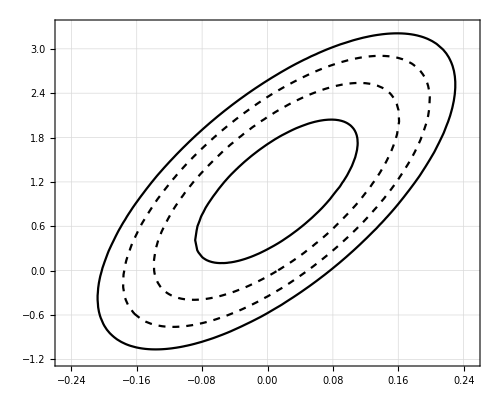

```mathematica
ContourPlot[{ΔKsKSim[ϵT,ϵR]==(2.1+3 0.4)/1.5-1,ΔKsKSim[ϵT,ϵR]==(2.1-3 0.4)/1.5-1,ΔKsKSim[ϵT,ϵR]==(2.1+0.4)/1.5-1,ΔKsKSim[ϵT,ϵR]==(2.1-0.4)/1.5-1},{ϵT,-.25,.25},{ϵR,-1.2,3.3},GridLines->Automatic,FrameLabel->{{MaTeX["\\epsilon_R",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX["\\tau^-\\to\\overline{K}^* K^-\\bar{\\nu}_{\\tau}",Magnification->1.5]}},ContourStyle->{Black,Black,{Dashed,Black},{Dashed,Black}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"ER_KsK.pdf"}],%]
```

/home/diego/ER_KsK.pdf

```mathematica
PltBr1=Plot[{ΔKsKSim[0.0,ϵR],(2.1+3 0.4)/1.5-1,(2.1-3 0.4)/1.5-1,(2.1+0.4)/1.5-1,(2.1-0.4)/1.5-1},{ϵR,-.8,2.7},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\Delta(\\tau^-\\to \\overline{K}^* K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_R",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Delta_KsK_1.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Delta_KsK_1.pdf

```mathematica
PltBr2=Plot[{ΔKsKSim[ϵT,0.0],(2.1+3 0.4)/1.5-1,(2.1-3 0.4)/1.5-1,(2.1+0.4)/1.5-1,(2.1-0.4)/1.5-1},{ϵT,-.22,.1},PlotStyle->{Blue,{Dashed,Black},{Dashed,Black},{DotDashed,Gray},{DotDashed,Gray}},FrameLabel->{{MaTeX["\\Delta(\\tau^-\\to \\overline{K}^* K^-\\bar{\\nu}_{\\tau})",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},GridLines->Automatic,PlotPoints->3];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Delta_KsK_2.pdf"}],%]
```

/home/diego/Dropbox/TautoOmegaK/Computation/Delta_KsK_2.pdf

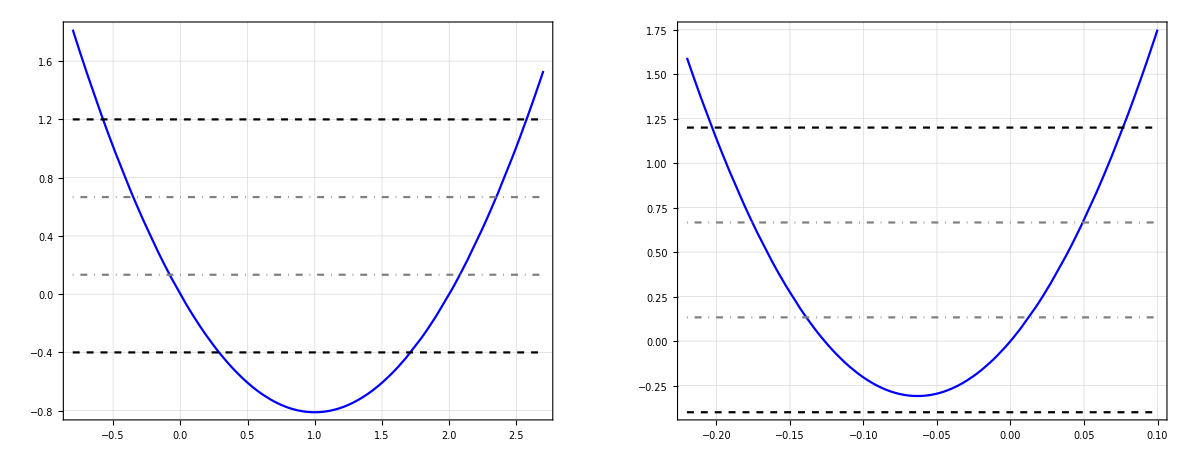

```mathematica
GraphicsRow[{PltBr1,PltBr2},ImageSize->1190]
```

### Com

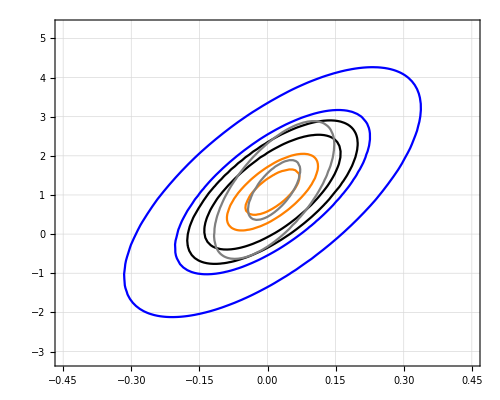

```mathematica
ContourPlot[{ΔKsKSim[ϵT,ϵR]==(2.1+ 0.4)/1.5-1,ΔKsKSim[ϵT,ϵR]==(2.1- 0.4)/1.5-1,ΔKsπSim[ϵT,ϵR]==(2.6+ 0.5)/5.1-1,ΔKsπSim[ϵT,ϵR]==(2.2- 0.5)/5.1-1,ΔρKSim[ϵT,ϵR]==(1.6+ 0.6)/(.47)-1,ΔρKSim[ϵT,ϵR]==(1.6- 0.6)/(.47)-1,ΔωKSim[ϵT,ϵR]==(4.1+3 0.9)/4.0-1,ΔωKSim[ϵT,ϵR]==(4.1-3 0.9)/4.0-1},{ϵT,-.45,.45},{ϵR,-3.2,5.3},GridLines->Automatic,FrameLabel->{{MaTeX["\\epsilon_R",Magnification->1.5]," "},{MaTeX["\\epsilon_T",Magnification->1.5],MaTeX[" ",Magnification->1.5]}},ContourStyle->{Black,Black,Orange,Orange,Blue,Blue,Gray,Gray}]
```